Grey  Wolf Optimizer Implementation

Defining  the function

```mathematica
fitnessSphere[x_]:=Total[x^2]
```

```mathematica
fitnessRastrigin[x_]:=10 Length[x]+Total[x^2-10 Cos[2 Pi x]]
```

```mathematica
fitnessRosenbrock[x_]:=Total[Table[100 (x[[i+1]]-x[[i]]^2)^2+(1-x[[i]])^2,{i,Length[x]-1}]]
```

Classifying  the Wolf

```mathematica
CreateWolf[fitness_,dim_,minx_,maxx_,seed_]:=Module[{position,rnd,wolf},
SeedRandom[seed];
position=Table[0.0,{dim}];
Do[position[[i]]=(maxx-minx) RandomReal[]+minx,{i,dim}];
fitnessValue=fitness[position];
wolf=<|"Position"->position,"Fitness"->fitnessValue|>;
wolf]
```

Grey  Wolf Optimization

```mathematica
gwo[fitness_,maxIter_,n_,dim_,minx_,maxx_]:=Module[{rnd,population,alphaWolf,betaWolf,gammaWolf,Iter,a,A1,A2,A3,C1,C2,C3,X1,X2,X3,Xnew,fnew},rnd=RandomReal[1,{n,dim}];
population=Table[<|"position"->RandomReal[{minx,maxx},dim],"fitness"->fitness[RandomReal[{minx,maxx},dim]]|>,{n}];
population=SortBy[population,#fitness&];
{alphaWolf,betaWolf,gammaWolf}=population[[;;3]];
Iter=0;
While[Iter<maxIter,If[Mod[Iter,10]==0&&Iter>1,Print["Iter = ",Iter," best fitness = ",alphaWolf["fitness"]]];
a=2 (1-Iter/maxIter);
Do[A1=a (2 RandomReal[]-1);
A2=a (2 RandomReal[]-1);
A3=a (2 RandomReal[]-1);
C1=2 RandomReal[];
C2=2 RandomReal[];
C3=2 RandomReal[];
X1=alphaWolf["position"]-A1 Abs[C1 alphaWolf["position"]-population[[i,"position"]]];
X2=betaWolf["position"]-A2 Abs[C2 betaWolf["position"]-population[[i,"position"]]];
X3=gammaWolf["position"]-A3 Abs[C3 gammaWolf["position"]-population[[i,"position"]]];
Xnew=Mean[{X1,X2,X3}];
fnew=fitness[Xnew];
If[fnew<population[[i,"fitness"]],population[[i,"position"]]=Xnew;
population[[i,"fitness"]]=fnew;],{i,n}];
population=SortBy[population,#fitness&];
{alphaWolf,betaWolf,gammaWolf}=population[[;;3]];
Iter++;];
alphaWolf["position"]];
```

Running  test for Sphere function

Case 01.01: Sphere function with dimension 2

```mathematica
dimension=2;
populationSizes={10,20,50,100};
iterationValues={10,30,50};
results2={};

Do[Do[Print["Running test for dimension=",dimension,", population_size=",populationSize,", num_iterations=",numIter];
bestSolutions=Table[gwo[fitnessSphere,numIter,populationSize,dimension,-10.0,10.0],{10}];
bestSolution=First[SortBy[bestSolutions,fitnessSphere]];
Print["Best Result for population_size=",populationSize,", num_iter=",numIter,": ",bestSolution," with fitness = ",fitnessSphere[bestSolution]];
AppendTo[results2,<|"Dimension"->dimension,"Population Size"->populationSize,"Iteration Number"->numIter,"Label"->"SpF"<>ToString[dimension]<>ToString[populationSize]<>ToString[numIter],"Solution"->bestSolution,"Fitness"->fitnessSphere[bestSolution]|>],{numIter,iterationValues}],{populationSize,populationSizes}];

spfDF=Dataset[results2];
Print[spfDF]
```

Running test for dimension=2, population_size=10, num_iterations=10

Best Result for population_size=10, num_iter=10: {-0.00679733,0.0373743} with fitness = 0.00144304

Running test for dimension=2, population_size=10, num_iterations=30

Iter = 10 best fitness = 0.000622119

Iter = 20 best fitness = 0.0000872077

Iter = 10 best fitness = 0.963157

Iter = 20 best fitness = 0.963157

Iter = 10 best fitness = 0.0507994

Iter = 20 best fitness = 0.0060998

Iter = 10 best fitness = 0.0339307

Iter = 20 best fitness = 0.00360136

Iter = 10 best fitness = 0.00359014

Iter = 20 best fitness = 0.0000614909

Iter = 10 best fitness = 0.0326437

Iter = 20 best fitness = 0.00217031

Iter = 10 best fitness = 0.000151521

Iter = 20 best fitness = 0.0000262621

Iter = 10 best fitness = 0.0155139

Iter = 20 best fitness = 0.00285856

Iter = 10 best fitness = 1.42145

Iter = 20 best fitness = 1.42145

Iter = 10 best fitness = 1.17669

Iter = 20 best fitness = 1.17669

Best Result for population_size=10, num_iter=30: {0.00302668,-0.00315727} with fitness = 0.0000191292

Running test for dimension=2, population_size=10, num_iterations=50

Iter = 10 best fitness = 0.0549742

Iter = 20 best fitness = 0.00520699

Iter = 30 best fitness = 0.000729663

Iter = 40 best fitness = 0.000462292

Iter = 10 best fitness = 0.0000187255

Iter = 20 best fitness = 1.03438×10^-10

Iter = 30 best fitness = 1.86737×10^-11

Iter = 40 best fitness = 1.07818×10^-11

Iter = 10 best fitness = 0.000174542

Iter = 20 best fitness = 4.50912×10^-6

Iter = 30 best fitness = 7.54841×10^-7

Iter = 40 best fitness = 3.98816×10^-7

Iter = 10 best fitness = 0.502846

Iter = 20 best fitness = 0.502846

Iter = 30 best fitness = 0.502846

Iter = 40 best fitness = 0.502846

Iter = 10 best fitness = 0.00095779

Iter = 20 best fitness = 1.02981×10^-6

Iter = 30 best fitness = 1.13713×10^-7

Iter = 40 best fitness = 4.63737×10^-8

Iter = 10 best fitness = 0.00107909

Iter = 20 best fitness = 0.000117494

Iter = 30 best fitness = 0.0000239768

Iter = 40 best fitness = 0.0000106481

Iter = 10 best fitness = 0.000587481

Iter = 20 best fitness = 0.0000161364

Iter = 30 best fitness = 2.35098×10^-6

Iter = 40 best fitness = 1.45823×10^-6

Iter = 10 best fitness = 0.00537695

Iter = 20 best fitness = 0.0000627987

Iter = 30 best fitness = 0.0000199953

Iter = 40 best fitness = 0.0000107376

Iter = 10 best fitness = 0.100361

Iter = 20 best fitness = 0.00982511

Iter = 30 best fitness = 0.00167095

Iter = 40 best fitness = 0.000753224

Iter = 10 best fitness = 0.0345904

Iter = 20 best fitness = 0.00235951

Iter = 30 best fitness = 0.000799759

Iter = 40 best fitness = 0.000370855

Best Result for population_size=10, num_iter=50: {2.14848×10^-6,-2.17124×10^-6} with fitness = 9.33022×10^-12

Running test for dimension=2, population_size=20, num_iterations=10

Best Result for population_size=20, num_iter=10: {-0.00422049,0.0227138} with fitness = 0.000533731

Running test for dimension=2, population_size=20, num_iterations=30

Iter = 10 best fitness = 1.60409

Iter = 20 best fitness = 1.60409

Iter = 10 best fitness = 0.510255

Iter = 20 best fitness = 0.510255

Iter = 10 best fitness = 0.000231696

Iter = 20 best fitness = 1.7349×10^-7

Iter = 10 best fitness = 0.00129326

Iter = 20 best fitness = 0.0000393753

Iter = 10 best fitness = 0.0697476

Iter = 20 best fitness = 0.0697476

Iter = 10 best fitness = 0.00120487

Iter = 20 best fitness = 6.60191×10^-6

Iter = 10 best fitness = 8.19046×10^-6

Iter = 20 best fitness = 5.47521×10^-8

Iter = 10 best fitness = 0.000250286

Iter = 20 best fitness = 0.0000159825

Iter = 10 best fitness = 0.000243869

Iter = 20 best fitness = 0.0000102634

Iter = 10 best fitness = 0.00235228

Iter = 20 best fitness = 0.0000125277

Best Result for population_size=20, num_iter=30: {0.000128834,-0.000133263} with fitness = 3.43572×10^-8

Running test for dimension=2, population_size=20, num_iterations=50

Iter = 10 best fitness = 0.00131422

Iter = 20 best fitness = 6.85408×10^-11

Iter = 30 best fitness = 2.85988×10^-12

Iter = 40 best fitness = 1.08571×10^-12

Iter = 10 best fitness = 0.000389592

Iter = 20 best fitness = 9.26248×10^-7

Iter = 30 best fitness = 5.74774×10^-8

Iter = 40 best fitness = 1.94211×10^-8

Iter = 10 best fitness = 0.000063251

Iter = 20 best fitness = 1.51182×10^-7

Iter = 30 best fitness = 9.71786×10^-9

Iter = 40 best fitness = 4.56584×10^-9

Iter = 10 best fitness = 0.0126188

Iter = 20 best fitness = 0.000131103

Iter = 30 best fitness = 0.0000205343

Iter = 40 best fitness = 7.08923×10^-6

Iter = 10 best fitness = 2.21808×10^-6

Iter = 20 best fitness = 5.8662×10^-10

Iter = 30 best fitness = 9.07257×10^-12

Iter = 40 best fitness = 3.6702×10^-12

Iter = 10 best fitness = 1.6676

Iter = 20 best fitness = 1.64474

Iter = 30 best fitness = 1.64474

Iter = 40 best fitness = 1.64474

Iter = 10 best fitness = 0.0000597682

Iter = 20 best fitness = 6.98431×10^-9

Iter = 30 best fitness = 2.17854×10^-10

Iter = 40 best fitness = 7.59647×10^-11

Iter = 10 best fitness = 2.48259×10^-6

Iter = 20 best fitness = 8.32756×10^-9

Iter = 30 best fitness = 4.33778×10^-10

Iter = 40 best fitness = 1.82971×10^-10

Iter = 10 best fitness = 2.80968

Iter = 20 best fitness = 0.193782

Iter = 30 best fitness = 0.0238448

Iter = 40 best fitness = 0.00792114

Iter = 10 best fitness = 0.0000491885

Iter = 20 best fitness = 2.96165×10^-7

Iter = 30 best fitness = 2.97584×10^-8

Iter = 40 best fitness = 1.17022×10^-8

Best Result for population_size=20, num_iter=50: {6.51179×10^-7,-6.71181×10^-7} with fitness = 8.74519×10^-13

Running test for dimension=2, population_size=50, num_iterations=10

Best Result for population_size=50, num_iter=10: {-2.70338×10^-6,-3.79988×10^-6} with fitness = 2.17473×10^-11

Running test for dimension=2, population_size=50, num_iterations=30

Iter = 10 best fitness = 0.000494987

Iter = 20 best fitness = 3.21527×10^-7

Iter = 10 best fitness = 0.000877225

Iter = 20 best fitness = 2.1159×10^-6

Iter = 10 best fitness = 1.37272

Iter = 20 best fitness = 1.37272

Iter = 10 best fitness = 0.0767341

Iter = 20 best fitness = 0.000226704

Iter = 10 best fitness = 2.04997×10^-8

Iter = 20 best fitness = 4.0846×10^-11

Iter = 10 best fitness = 0.164759

Iter = 20 best fitness = 0.164759

Iter = 10 best fitness = 2.24258×10^-9

Iter = 20 best fitness = 1.11702×10^-12

Iter = 10 best fitness = 5.45766×10^-7

Iter = 20 best fitness = 5.7022×10^-15

Iter = 10 best fitness = 5.80955×10^-6

Iter = 20 best fitness = 5.57334×10^-9

Iter = 10 best fitness = 3.32618×10^-8

Iter = 20 best fitness = 6.46566×10^-13

Best Result for population_size=50, num_iter=30: {-3.06309×10^-8,3.03518×10^-8} with fitness = 1.85949×10^-15

Running test for dimension=2, population_size=50, num_iterations=50

Iter = 10 best fitness = 5.02943×10^-7

Iter = 20 best fitness = 4.36455×10^-12

Iter = 30 best fitness = 2.0806×10^-14

Iter = 40 best fitness = 4.98537×10^-15

Iter = 10 best fitness = 0.406845

Iter = 20 best fitness = 0.406845

Iter = 30 best fitness = 0.406845

Iter = 40 best fitness = 0.406845

Iter = 10 best fitness = 9.7346×10^-7

Iter = 20 best fitness = 6.99718×10^-11

Iter = 30 best fitness = 3.08686×10^-13

Iter = 40 best fitness = 5.97609×10^-14

Iter = 10 best fitness = 6.5898×10^-6

Iter = 20 best fitness = 3.76535×10^-15

Iter = 30 best fitness = 3.36831×10^-18

Iter = 40 best fitness = 6.38256×10^-19

Iter = 10 best fitness = 4.40149×10^-7

Iter = 20 best fitness = 2.75609×10^-15

Iter = 30 best fitness = 5.39931×10^-20

Iter = 40 best fitness = 1.18033×10^-20

Iter = 10 best fitness = 0.0000128905

Iter = 20 best fitness = 1.28187×10^-9

Iter = 30 best fitness = 3.17579×10^-12

Iter = 40 best fitness = 7.10183×10^-13

Iter = 10 best fitness = 1.76242×10^-6

Iter = 20 best fitness = 1.75026×10^-10

Iter = 30 best fitness = 3.73181×10^-13

Iter = 40 best fitness = 1.09945×10^-13

Iter = 10 best fitness = 0.000172569

Iter = 20 best fitness = 7.38506×10^-14

Iter = 30 best fitness = 2.02719×10^-16

Iter = 40 best fitness = 3.42584×10^-17

Iter = 10 best fitness = 4.84527×10^-6

Iter = 20 best fitness = 1.90078×10^-15

Iter = 30 best fitness = 7.07122×10^-20

Iter = 40 best fitness = 1.17171×10^-20

Iter = 10 best fitness = 6.93909×10^-8

Iter = 20 best fitness = 2.04532×10^-12

Iter = 30 best fitness = 6.5087×10^-14

Iter = 40 best fitness = 9.11484×10^-15

Best Result for population_size=50, num_iter=50: {-6.37805×10^-11,6.59564×10^-11} with fitness = 8.4182×10^-21

Running test for dimension=2, population_size=100, num_iterations=10

Best Result for population_size=100, num_iter=10: {3.33399×10^-6,-3.09612×10^-6} with fitness = 2.07014×10^-11

Running test for dimension=2, population_size=100, num_iterations=30

Iter = 10 best fitness = 5.43696×10^-10

Iter = 20 best fitness = 5.32979×10^-17

Iter = 10 best fitness = 5.68306×10^-8

Iter = 20 best fitness = 1.50574×10^-13

Iter = 10 best fitness = 2.43077×10^-10

Iter = 20 best fitness = 6.31633×10^-14

Iter = 10 best fitness = 0.0955808

Iter = 20 best fitness = 0.0955808

Iter = 10 best fitness = 0.0549179

Iter = 20 best fitness = 3.03737×10^-11

Iter = 10 best fitness = 0.109065

Iter = 20 best fitness = 0.109065

Iter = 10 best fitness = 7.0264×10^-8

Iter = 20 best fitness = 1.87281×10^-16

Iter = 10 best fitness = 7.2376×10^-10

Iter = 20 best fitness = 1.9955×10^-18

Iter = 10 best fitness = 4.79489×10^-8

Iter = 20 best fitness = 1.46389×10^-16

Iter = 10 best fitness = 0.293219

Iter = 20 best fitness = 0.293219

Best Result for population_size=100, num_iter=30: {3.89674×10^-10,-3.85842×10^-10} with fitness = 3.0072×10^-19

Running test for dimension=2, population_size=100, num_iterations=50

Iter = 10 best fitness = 9.07733×10^-10

Iter = 20 best fitness = 2.01672×10^-17

Iter = 30 best fitness = 3.40114×10^-21

Iter = 40 best fitness = 2.67454×10^-22

Iter = 10 best fitness = 7.53062×10^-8

Iter = 20 best fitness = 4.37239×10^-17

Iter = 30 best fitness = 4.44086×10^-20

Iter = 40 best fitness = 2.54357×10^-21

Iter = 10 best fitness = 5.37911×10^-9

Iter = 20 best fitness = 4.12411×10^-16

Iter = 30 best fitness = 3.96107×10^-30

Iter = 40 best fitness = 1.79114×10^-33

Iter = 10 best fitness = 3.36504×10^-7

Iter = 20 best fitness = 3.08617×10^-19

Iter = 30 best fitness = 5.55216×10^-23

Iter = 40 best fitness = 5.84435×10^-24

Iter = 10 best fitness = 3.85332×10^-10

Iter = 20 best fitness = 6.85914×10^-19

Iter = 30 best fitness = 1.02178×10^-22

Iter = 40 best fitness = 7.42843×10^-24

Iter = 10 best fitness = 1.02243×10^-10

Iter = 20 best fitness = 4.59149×10^-15

Iter = 30 best fitness = 6.21819×10^-18

Iter = 40 best fitness = 6.50076×10^-19

Iter = 10 best fitness = 5.40533×10^-10

Iter = 20 best fitness = 2.35753×10^-19

Iter = 30 best fitness = 1.05346×10^-24

Iter = 40 best fitness = 1.44031×10^-25

Iter = 10 best fitness = 3.98663×10^-9

Iter = 20 best fitness = 8.34558×10^-15

Iter = 30 best fitness = 1.4726×10^-19

Iter = 40 best fitness = 1.6906×10^-20

Iter = 10 best fitness = 0.882586

Iter = 20 best fitness = 0.882586

Iter = 30 best fitness = 0.882586

Iter = 40 best fitness = 0.882586

Iter = 10 best fitness = 7.10572×10^-12

Iter = 20 best fitness = 2.17087×10^-22

Iter = 30 best fitness = 1.09943×10^-31

Iter = 40 best fitness = 2.00377×10^-39

Best Result for population_size=100, num_iter=50: {-2.63793×10^-20,2.61681×10^-20} with fitness = 1.38064×10^-39

Case 01.02: Sphere function with dimension 5

```mathematica
dimension=5;
populationSizes={10,20,50,100};
iterationValues={10,30,50};
results5={};

Do[Do[Print["Running test for dimension=",dimension,", population_size=",populationSize,", num_iterations=",numIter];
bestSolutions=Table[gwo[fitnessSphere,numIter,populationSize,dimension,-10.0,10.0],{10}];
bestSolution=First[SortBy[bestSolutions,fitnessSphere]];
Print["Best Result for population_size=",populationSize,", num_iter=",numIter,": ",bestSolution," with fitness = ",fitnessSphere[bestSolution]];
AppendTo[results5,<|"Dimension"->dimension,"Population Size"->populationSize,"Iteration Number"->numIter,"Label"->"SpF"<>ToString[dimension]<>ToString[populationSize]<>ToString[numIter],"Solution"->bestSolution,"Fitness"->fitnessSphere[bestSolution]|>],{numIter,iterationValues}],{populationSize,populationSizes}];

spfDF=Dataset[Join[Normal[spfDF],results5]];
Print[spfDF]
```

Running test for dimension=5, population_size=10, num_iterations=10

Best Result for population_size=10, num_iter=10: {0.173511,-0.314882,0.275779,0.144957,-0.132803} with fitness = 0.24396

Running test for dimension=5, population_size=10, num_iterations=30

Iter = 10 best fitness = 1.79548

Iter = 20 best fitness = 0.27103

Iter = 10 best fitness = 0.598025

Iter = 20 best fitness = 0.0986531

Iter = 10 best fitness = 0.977262

Iter = 20 best fitness = 0.15049

Iter = 10 best fitness = 0.406162

Iter = 20 best fitness = 0.0490953

Iter = 10 best fitness = 2.9645

Iter = 20 best fitness = 0.505667

Iter = 10 best fitness = 1.39266

Iter = 20 best fitness = 0.214808

Iter = 10 best fitness = 66.6786

Iter = 20 best fitness = 66.6786

Iter = 10 best fitness = 24.8114

Iter = 20 best fitness = 7.9054

Iter = 10 best fitness = 2.17504

Iter = 20 best fitness = 0.0900868

Iter = 10 best fitness = 1.28268

Iter = 20 best fitness = 0.153662

Best Result for population_size=10, num_iter=30: {0.052588,-0.0108958,0.101986,0.0667524,-0.133218} with fitness = 0.0354883

Running test for dimension=5, population_size=10, num_iterations=50

Iter = 10 best fitness = 0.819746

Iter = 20 best fitness = 0.0186215

Iter = 30 best fitness = 0.00423919

Iter = 40 best fitness = 0.00244015

Iter = 10 best fitness = 2.72754

Iter = 20 best fitness = 0.0784011

Iter = 30 best fitness = 0.019363

Iter = 40 best fitness = 0.00971345

Iter = 10 best fitness = 3.62924

Iter = 20 best fitness = 0.254749

Iter = 30 best fitness = 0.0427651

Iter = 40 best fitness = 0.0168015

Iter = 10 best fitness = 1.68735

Iter = 20 best fitness = 0.0251541

Iter = 30 best fitness = 0.00124035

Iter = 40 best fitness = 0.000846874

Iter = 10 best fitness = 0.251676

Iter = 20 best fitness = 0.0272332

Iter = 30 best fitness = 0.00652303

Iter = 40 best fitness = 0.00360861

Iter = 10 best fitness = 31.9348

Iter = 20 best fitness = 31.9348

Iter = 30 best fitness = 31.9348

Iter = 40 best fitness = 31.9348

Iter = 10 best fitness = 1.42299

Iter = 20 best fitness = 0.00771195

Iter = 30 best fitness = 0.00126312

Iter = 40 best fitness = 0.000563867

Iter = 10 best fitness = 4.04225

Iter = 20 best fitness = 0.161838

Iter = 30 best fitness = 0.0400717

Iter = 40 best fitness = 0.0187895

Iter = 10 best fitness = 0.529716

Iter = 20 best fitness = 0.0768661

Iter = 30 best fitness = 0.00774985

Iter = 40 best fitness = 0.00320803

Iter = 10 best fitness = 4.30933

Iter = 20 best fitness = 0.471547

Iter = 30 best fitness = 0.125198

Iter = 40 best fitness = 0.0749256

Best Result for population_size=10, num_iter=50: {0.00254719,0.0150143,0.00172643,0.00491958,-0.0163601} with fitness = 0.000526752

Running test for dimension=5, population_size=20, num_iterations=10

Best Result for population_size=20, num_iter=10: {-0.0246571,-0.343599,0.108477,0.343773,0.32129} with fitness = 0.351842

Running test for dimension=5, population_size=20, num_iterations=30

Iter = 10 best fitness = 2.57819

Iter = 20 best fitness = 0.12848

Iter = 10 best fitness = 0.031869

Iter = 20 best fitness = 0.00218498

Iter = 10 best fitness = 0.0228001

Iter = 20 best fitness = 0.00230471

Iter = 10 best fitness = 0.185781

Iter = 20 best fitness = 0.00610566

Iter = 10 best fitness = 0.759868

Iter = 20 best fitness = 0.0699685

Iter = 10 best fitness = 0.0135226

Iter = 20 best fitness = 0.000844121

Iter = 10 best fitness = 0.0359073

Iter = 20 best fitness = 0.000229926

Iter = 10 best fitness = 41.4953

Iter = 20 best fitness = 41.4953

Iter = 10 best fitness = 20.1108

Iter = 20 best fitness = 20.1108

Iter = 10 best fitness = 0.113348

Iter = 20 best fitness = 0.00164707

Best Result for population_size=20, num_iter=30: {0.00816707,-0.000393383,-0.00615953,-0.00364322,-0.00374573} with fitness = 0.000132099

Running test for dimension=5, population_size=20, num_iterations=50

Iter = 10 best fitness = 0.00971338

Iter = 20 best fitness = 0.000114664

Iter = 30 best fitness = 2.95123×10^-6

Iter = 40 best fitness = 1.34057×10^-6

Iter = 10 best fitness = 0.0574864

Iter = 20 best fitness = 0.000176056

Iter = 30 best fitness = 0.0000191548

Iter = 40 best fitness = 4.20647×10^-6

Iter = 10 best fitness = 0.00272706

Iter = 20 best fitness = 0.0000138818

Iter = 30 best fitness = 8.42703×10^-7

Iter = 40 best fitness = 2.96831×10^-7

Iter = 10 best fitness = 0.158211

Iter = 20 best fitness = 0.00268418

Iter = 30 best fitness = 0.000066458

Iter = 40 best fitness = 0.000023719

Iter = 10 best fitness = 0.0330931

Iter = 20 best fitness = 0.000188849

Iter = 30 best fitness = 0.0000206616

Iter = 40 best fitness = 6.14504×10^-6

Iter = 10 best fitness = 17.7411

Iter = 20 best fitness = 14.637

Iter = 30 best fitness = 14.637

Iter = 40 best fitness = 14.637

Iter = 10 best fitness = 24.5821

Iter = 20 best fitness = 24.5821

Iter = 30 best fitness = 24.5821

Iter = 40 best fitness = 24.5821

Iter = 10 best fitness = 0.0858545

Iter = 20 best fitness = 0.000731997

Iter = 30 best fitness = 0.0000530118

Iter = 40 best fitness = 0.0000177717

Iter = 10 best fitness = 0.730943

Iter = 20 best fitness = 0.00257385

Iter = 30 best fitness = 0.0000150924

Iter = 40 best fitness = 5.30296×10^-6

Iter = 10 best fitness = 0.0457511

Iter = 20 best fitness = 0.00039832

Iter = 30 best fitness = 0.0000108926

Iter = 40 best fitness = 4.37541×10^-6

Best Result for population_size=20, num_iter=50: {0.000354718,-0.0000192088,-0.0000477461,-0.000348396,-0.0000547257} with fitness = 2.52848×10^-7

Running test for dimension=5, population_size=50, num_iterations=10

Best Result for population_size=50, num_iter=10: {0.0138508,-0.0804529,-0.116152,0.146352,0.0581636} with fitness = 0.0449576

Running test for dimension=5, population_size=50, num_iterations=30

Iter = 10 best fitness = 0.016398

Iter = 20 best fitness = 0.000170283

Iter = 10 best fitness = 0.129964

Iter = 20 best fitness = 0.000753204

Iter = 10 best fitness = 0.00633183

Iter = 20 best fitness = 0.0000474509

Iter = 10 best fitness = 0.00346513

Iter = 20 best fitness = 0.0000105957

Iter = 10 best fitness = 0.0187551

Iter = 20 best fitness = 0.000260989

Iter = 10 best fitness = 3.38073

Iter = 20 best fitness = 3.38073

Iter = 10 best fitness = 0.0157721

Iter = 20 best fitness = 0.000147057

Iter = 10 best fitness = 0.00888879

Iter = 20 best fitness = 0.0000350049

Iter = 10 best fitness = 0.0428892

Iter = 20 best fitness = 0.000704444

Iter = 10 best fitness = 0.000490807

Iter = 20 best fitness = 3.74691×10^-6

Best Result for population_size=50, num_iter=30: {0.000575457,-0.000221356,-0.000943375,0.000776777,-0.0000130613} with fitness = 1.87366×10^-6

Running test for dimension=5, population_size=50, num_iterations=50

Iter = 10 best fitness = 0.00665175

Iter = 20 best fitness = 0.000015572

Iter = 30 best fitness = 4.39767×10^-7

Iter = 40 best fitness = 9.51482×10^-8

Iter = 10 best fitness = 0.0000954643

Iter = 20 best fitness = 4.90195×10^-7

Iter = 30 best fitness = 2.04757×10^-8

Iter = 40 best fitness = 4.51539×10^-9

Iter = 10 best fitness = 0.00326283

Iter = 20 best fitness = 7.05595×10^-7

Iter = 30 best fitness = 5.7538×10^-9

Iter = 40 best fitness = 1.31322×10^-9

Iter = 10 best fitness = 0.000508632

Iter = 20 best fitness = 3.38315×10^-8

Iter = 30 best fitness = 5.37737×10^-10

Iter = 40 best fitness = 9.58495×10^-11

Iter = 10 best fitness = 0.00786519

Iter = 20 best fitness = 6.52938×10^-6

Iter = 30 best fitness = 8.56868×10^-8

Iter = 40 best fitness = 1.2961×10^-8

Iter = 10 best fitness = 0.00243803

Iter = 20 best fitness = 3.12121×10^-6

Iter = 30 best fitness = 1.94098×10^-8

Iter = 40 best fitness = 3.81425×10^-9

Iter = 10 best fitness = 0.014156

Iter = 20 best fitness = 8.77241×10^-7

Iter = 30 best fitness = 9.83188×10^-9

Iter = 40 best fitness = 1.58243×10^-9

Iter = 10 best fitness = 0.00161649

Iter = 20 best fitness = 5.70184×10^-7

Iter = 30 best fitness = 4.89267×10^-9

Iter = 40 best fitness = 1.2008×10^-9

Iter = 10 best fitness = 0.00386283

Iter = 20 best fitness = 1.01498×10^-7

Iter = 30 best fitness = 4.30397×10^-10

Iter = 40 best fitness = 6.43375×10^-11

Iter = 10 best fitness = 0.000462897

Iter = 20 best fitness = 5.17667×10^-8

Iter = 30 best fitness = 4.67688×10^-10

Iter = 40 best fitness = 1.00719×10^-10

Best Result for population_size=50, num_iter=50: {-3.17356×10^-6,-3.43056×10^-6,3.95209×10^-6,3.13144×10^-6,-1.85757×10^-6} with fitness = 5.07158×10^-11

Running test for dimension=5, population_size=100, num_iterations=10

Best Result for population_size=100, num_iter=10: {0.0543579,-0.0357024,-0.04535,0.00555381,-0.014966} with fitness = 0.00654089

Running test for dimension=5, population_size=100, num_iterations=30

Iter = 10 best fitness = 0.00889663

Iter = 20 best fitness = 9.09583×10^-6

Iter = 10 best fitness = 0.000840164

Iter = 20 best fitness = 9.52901×10^-7

Iter = 10 best fitness = 0.14034

Iter = 20 best fitness = 0.0000245552

Iter = 10 best fitness = 0.182724

Iter = 20 best fitness = 0.00102962

Iter = 10 best fitness = 0.00227866

Iter = 20 best fitness = 4.13446×10^-6

Iter = 10 best fitness = 0.000244995

Iter = 20 best fitness = 4.16855×10^-7

Iter = 10 best fitness = 0.00200147

Iter = 20 best fitness = 1.95683×10^-6

Iter = 10 best fitness = 0.385387

Iter = 20 best fitness = 0.000476246

Iter = 10 best fitness = 0.00119241

Iter = 20 best fitness = 8.9263×10^-7

Iter = 10 best fitness = 22.2872

Iter = 20 best fitness = 22.2872

Best Result for population_size=100, num_iter=30: {0.000252119,-0.000130853,-0.00023696,-0.0000511753,0.000111481} with fitness = 1.51883×10^-7

Running test for dimension=5, population_size=100, num_iterations=50

Iter = 10 best fitness = 0.00553607

Iter = 20 best fitness = 6.14815×10^-8

Iter = 30 best fitness = 8.05978×10^-11

Iter = 40 best fitness = 1.12989×10^-11

Iter = 10 best fitness = 0.00245212

Iter = 20 best fitness = 7.072×10^-8

Iter = 30 best fitness = 8.67411×10^-11

Iter = 40 best fitness = 1.29284×10^-11

Iter = 10 best fitness = 0.0000535811

Iter = 20 best fitness = 1.51529×10^-9

Iter = 30 best fitness = 2.15036×10^-12

Iter = 40 best fitness = 3.27818×10^-13

Iter = 10 best fitness = 0.0018351

Iter = 20 best fitness = 3.23479×10^-7

Iter = 30 best fitness = 1.23901×10^-10

Iter = 40 best fitness = 8.6396×10^-12

Iter = 10 best fitness = 0.000467929

Iter = 20 best fitness = 1.03018×10^-8

Iter = 30 best fitness = 4.10201×10^-11

Iter = 40 best fitness = 8.1544×10^-12

Iter = 10 best fitness = 0.00227728

Iter = 20 best fitness = 2.87715×10^-7

Iter = 30 best fitness = 7.24649×10^-10

Iter = 40 best fitness = 1.05619×10^-10

Iter = 10 best fitness = 0.000568579

Iter = 20 best fitness = 1.78633×10^-8

Iter = 30 best fitness = 5.12877×10^-11

Iter = 40 best fitness = 8.75437×10^-12

Iter = 10 best fitness = 0.000866651

Iter = 20 best fitness = 7.40978×10^-9

Iter = 30 best fitness = 1.58763×10^-11

Iter = 40 best fitness = 1.32061×10^-12

Iter = 10 best fitness = 0.000487657

Iter = 20 best fitness = 2.99974×10^-8

Iter = 30 best fitness = 6.89195×10^-11

Iter = 40 best fitness = 8.77632×10^-12

Iter = 10 best fitness = 0.000105533

Iter = 20 best fitness = 3.86401×10^-9

Iter = 30 best fitness = 3.43468×10^-12

Iter = 40 best fitness = 4.09782×10^-13

Best Result for population_size=100, num_iter=50: {1.89637×10^-7,1.57678×10^-8,-3.44956×10^-7,3.54406×10^-8,2.88381×10^-7} with fitness = 2.39625×10^-13

Case 01.03: Sphere function with dimension 10

```mathematica
dimension=10;
populationSizes={10,20,50,100};
iterationValues={10,30,50};
results10={};

Do[Do[Print["Running test for dimension=",dimension,", population_size=",populationSize,", num_iterations=",numIter];
bestSolutions=Table[gwo[fitnessSphere,numIter,populationSize,dimension,-10.0,10.0],{10}];
bestSolution=First[SortBy[bestSolutions,fitnessSphere]];
Print["Best Result for population_size=",populationSize,", num_iter=",numIter,": ",bestSolution," with fitness = ",fitnessSphere[bestSolution]];
AppendTo[results10,<|"Dimension"->dimension,"Population Size"->populationSize,"Iteration Number"->numIter,"Label"->"SpF"<>ToString[dimension]<>ToString[populationSize]<>ToString[numIter],"Solution"->bestSolution,"Fitness"->fitnessSphere[bestSolution]|>],{numIter,iterationValues}],{populationSize,populationSizes}];

spfDF=Dataset[Join[Normal[spfDF],results10]];
Print[spfDF]
```

Running test for dimension=10, population_size=10, num_iterations=10

Best Result for population_size=10, num_iter=10: {0.583384,-1.26765,0.0694385,0.837762,0.454627,-0.215978,-0.192113,0.201044,0.324376,-0.230134} with fitness = 3.14278

Running test for dimension=10, population_size=10, num_iterations=30

Iter = 10 best fitness = 8.03577

Iter = 20 best fitness = 0.892485

Iter = 10 best fitness = 2.17575

Iter = 20 best fitness = 0.492773

Iter = 10 best fitness = 25.0095

Iter = 20 best fitness = 6.11306

Iter = 10 best fitness = 2.35429

Iter = 20 best fitness = 0.0855563

Iter = 10 best fitness = 12.9511

Iter = 20 best fitness = 1.18848

Iter = 10 best fitness = 24.0085

Iter = 20 best fitness = 5.48135

Iter = 10 best fitness = 1.03257

Iter = 20 best fitness = 0.159091

Iter = 10 best fitness = 9.10403

Iter = 20 best fitness = 0.732125

Iter = 10 best fitness = 19.9562

Iter = 20 best fitness = 6.86129

Iter = 10 best fitness = 5.18135

Iter = 20 best fitness = 0.467461

Best Result for population_size=10, num_iter=30: {-0.00356593,0.0789326,0.0658089,0.1131,-0.000874583,0.0363461,0.0241179,-0.171241,0.0819826,-0.0689391} with fitness = 0.0660663

Running test for dimension=10, population_size=10, num_iterations=50

Iter = 10 best fitness = 0.928

Iter = 20 best fitness = 0.0995733

Iter = 30 best fitness = 0.0271203

Iter = 40 best fitness = 0.0169644

Iter = 10 best fitness = 12.7332

Iter = 20 best fitness = 0.54101

Iter = 30 best fitness = 0.211938

Iter = 40 best fitness = 0.126254

Iter = 10 best fitness = 0.825604

Iter = 20 best fitness = 0.077984

Iter = 30 best fitness = 0.0178556

Iter = 40 best fitness = 0.00900807

Iter = 10 best fitness = 7.62864

Iter = 20 best fitness = 0.0629653

Iter = 30 best fitness = 0.00828997

Iter = 40 best fitness = 0.00489874

Iter = 10 best fitness = 2.34648

Iter = 20 best fitness = 0.0610495

Iter = 30 best fitness = 0.00310773

Iter = 40 best fitness = 0.00156654

Iter = 10 best fitness = 2.37139

Iter = 20 best fitness = 0.293404

Iter = 30 best fitness = 0.0600501

Iter = 40 best fitness = 0.0306577

Iter = 10 best fitness = 9.50156

Iter = 20 best fitness = 0.339474

Iter = 30 best fitness = 0.0683779

Iter = 40 best fitness = 0.0370442

Iter = 10 best fitness = 5.96959

Iter = 20 best fitness = 0.169197

Iter = 30 best fitness = 0.034807

Iter = 40 best fitness = 0.0181129

Iter = 10 best fitness = 9.90674

Iter = 20 best fitness = 0.0857454

Iter = 30 best fitness = 0.0197715

Iter = 40 best fitness = 0.0121266

Iter = 10 best fitness = 2.84633

Iter = 20 best fitness = 0.0766122

Iter = 30 best fitness = 0.00774148

Iter = 40 best fitness = 0.00370093

Best Result for population_size=10, num_iter=50: {-0.00388504,-0.00111733,0.00324615,0.0030062,-0.000663092,-0.0204817,0.0242411,0.0100802,-0.0074527,-0.0134786} with fitness = 0.00138231

Running test for dimension=10, population_size=20, num_iterations=10

Best Result for population_size=20, num_iter=10: {0.294721,-0.252774,-0.073369,-1.013,-0.0666318,-0.135166,-0.0242743,1.03625,0.493762,0.00845731} with fitness = 2.52328

Running test for dimension=10, population_size=20, num_iterations=30

Iter = 10 best fitness = 2.90011

Iter = 20 best fitness = 0.166316

Iter = 10 best fitness = 1.10979

Iter = 20 best fitness = 0.062171

Iter = 10 best fitness = 2.23079

Iter = 20 best fitness = 0.1027

Iter = 10 best fitness = 14.0924

Iter = 20 best fitness = 0.571176

Iter = 10 best fitness = 0.387044

Iter = 20 best fitness = 0.015823

Iter = 10 best fitness = 1.02924

Iter = 20 best fitness = 0.00465718

Iter = 10 best fitness = 118.739

Iter = 20 best fitness = 118.739

Iter = 10 best fitness = 2.8916

Iter = 20 best fitness = 0.135664

Iter = 10 best fitness = 0.525018

Iter = 20 best fitness = 0.0179868

Iter = 10 best fitness = 0.772321

Iter = 20 best fitness = 0.0246334

Best Result for population_size=20, num_iter=30: {-0.0104484,0.0225773,-0.0192313,-0.011525,-0.0118543,0.0324699,-0.0197637,-0.0151019,-0.00437002,-0.0000964391} with fitness = 0.00295417

Running test for dimension=10, population_size=20, num_iterations=50

Iter = 10 best fitness = 91.755

Iter = 20 best fitness = 91.755

Iter = 30 best fitness = 91.755

Iter = 40 best fitness = 91.755

Iter = 10 best fitness = 1.64487

Iter = 20 best fitness = 0.00664501

Iter = 30 best fitness = 0.000448029

Iter = 40 best fitness = 0.000187133

Iter = 10 best fitness = 1.1869

Iter = 20 best fitness = 0.000624216

Iter = 30 best fitness = 0.0000300007

Iter = 40 best fitness = 0.0000116663

Iter = 10 best fitness = 4.22717

Iter = 20 best fitness = 0.0263488

Iter = 30 best fitness = 0.00327325

Iter = 40 best fitness = 0.000854391

Iter = 10 best fitness = 0.469243

Iter = 20 best fitness = 0.0142177

Iter = 30 best fitness = 0.000524455

Iter = 40 best fitness = 0.000152369

Iter = 10 best fitness = 1.31478

Iter = 20 best fitness = 0.00453468

Iter = 30 best fitness = 0.000179905

Iter = 40 best fitness = 0.0000731898

Iter = 10 best fitness = 0.914065

Iter = 20 best fitness = 0.00486562

Iter = 30 best fitness = 0.000322089

Iter = 40 best fitness = 0.000126362

Iter = 10 best fitness = 0.439062

Iter = 20 best fitness = 0.0085042

Iter = 30 best fitness = 0.000416425

Iter = 40 best fitness = 0.000170549

Iter = 10 best fitness = 0.730079

Iter = 20 best fitness = 0.00312845

Iter = 30 best fitness = 0.000192766

Iter = 40 best fitness = 0.0000747607

Iter = 10 best fitness = 1.71602

Iter = 20 best fitness = 0.00703943

Iter = 30 best fitness = 0.000103053

Iter = 40 best fitness = 0.0000343086

Best Result for population_size=20, num_iter=50: {-0.00214304,0.000283295,-0.000306032,0.00107047,-0.000128209,0.000492806,0.00184705,-0.000651386,0.000632537,-0.0000691286} with fitness = 0.0000104125

Running test for dimension=10, population_size=50, num_iterations=10

Best Result for population_size=50, num_iter=10: {0.160425,-0.10543,-0.0783032,0.254569,0.222263,0.48677,-0.487104,0.113426,0.286423,0.108004} with fitness = 0.737973

Running test for dimension=10, population_size=50, num_iterations=30

Iter = 10 best fitness = 0.111757

Iter = 20 best fitness = 0.000928861

Iter = 10 best fitness = 0.0565163

Iter = 20 best fitness = 0.000535244

Iter = 10 best fitness = 0.303453

Iter = 20 best fitness = 0.00111701

Iter = 10 best fitness = 0.179777

Iter = 20 best fitness = 0.000120709

Iter = 10 best fitness = 0.0195579

Iter = 20 best fitness = 0.0000697785

Iter = 10 best fitness = 0.379766

Iter = 20 best fitness = 0.00501057

Iter = 10 best fitness = 0.159316

Iter = 20 best fitness = 0.00155161

Iter = 10 best fitness = 0.116995

Iter = 20 best fitness = 0.000209307

Iter = 10 best fitness = 0.0186579

Iter = 20 best fitness = 0.000401157

Iter = 10 best fitness = 0.0870379

Iter = 20 best fitness = 0.00133021

Best Result for population_size=50, num_iter=30: {-0.0000988333,-0.0014535,0.00176527,0.000302193,-0.00243075,-0.00164259,0.000558615,-0.00109103,0.00162405,0.00244499} with fitness = 0.0000240545

Running test for dimension=10, population_size=50, num_iterations=50

Iter = 10 best fitness = 0.0807525

Iter = 20 best fitness = 0.0000544714

Iter = 30 best fitness = 2.76241×10^-7

Iter = 40 best fitness = 4.26956×10^-8

Iter = 10 best fitness = 40.1213

Iter = 20 best fitness = 0.000447201

Iter = 30 best fitness = 4.40987×10^-6

Iter = 40 best fitness = 9.11245×10^-7

Iter = 10 best fitness = 0.0660048

Iter = 20 best fitness = 4.98368×10^-6

Iter = 30 best fitness = 6.84265×10^-8

Iter = 40 best fitness = 1.22574×10^-8

Iter = 10 best fitness = 0.194941

Iter = 20 best fitness = 0.0000245664

Iter = 30 best fitness = 3.0104×10^-7

Iter = 40 best fitness = 5.9409×10^-8

Iter = 10 best fitness = 0.15368

Iter = 20 best fitness = 0.000112067

Iter = 30 best fitness = 1.57115×10^-6

Iter = 40 best fitness = 3.1052×10^-7

Iter = 10 best fitness = 0.0935371

Iter = 20 best fitness = 0.0000479246

Iter = 30 best fitness = 9.05405×10^-8

Iter = 40 best fitness = 1.665×10^-8

Iter = 10 best fitness = 1.96276

Iter = 20 best fitness = 0.00150626

Iter = 30 best fitness = 0.0000229337

Iter = 40 best fitness = 2.26998×10^-6

Iter = 10 best fitness = 1.50979

Iter = 20 best fitness = 0.000260243

Iter = 30 best fitness = 3.52131×10^-6

Iter = 40 best fitness = 6.77687×10^-7

Iter = 10 best fitness = 0.695822

Iter = 20 best fitness = 0.0000980875

Iter = 30 best fitness = 2.25387×10^-6

Iter = 40 best fitness = 3.98315×10^-7

Iter = 10 best fitness = 0.0106171

Iter = 20 best fitness = 0.0000614555

Iter = 30 best fitness = 1.31114×10^-6

Iter = 40 best fitness = 2.90989×10^-7

Best Result for population_size=50, num_iter=50: {0.0000173757,-3.48953×10^-6,-0.0000155035,-0.0000636612,7.71834×10^-6,-0.0000260509,0.0000378058,0.0000454543,-3.70096×10^-6,0.0000311274} with fitness = 9.82341×10^-9

Running test for dimension=10, population_size=100, num_iterations=10

Best Result for population_size=100, num_iter=10: {-0.0402338,-0.0398709,0.22118,0.110805,0.0306645,0.0155017,0.161564,-0.168118,-0.0944357,-0.186661} with fitness = 0.163715

Running test for dimension=10, population_size=100, num_iterations=30

Iter = 10 best fitness = 0.0920825

Iter = 20 best fitness = 0.000793203

Iter = 10 best fitness = 0.0200751

Iter = 20 best fitness = 0.0000118799

Iter = 10 best fitness = 0.0352679

Iter = 20 best fitness = 0.0000578146

Iter = 10 best fitness = 0.00392426

Iter = 20 best fitness = 3.22784×10^-6

Iter = 10 best fitness = 0.0131704

Iter = 20 best fitness = 6.55418×10^-6

Iter = 10 best fitness = 0.0142267

Iter = 20 best fitness = 0.000122273

Iter = 10 best fitness = 0.0592238

Iter = 20 best fitness = 0.000185004

Iter = 10 best fitness = 0.0314309

Iter = 20 best fitness = 0.0000991332

Iter = 10 best fitness = 0.00527922

Iter = 20 best fitness = 4.34347×10^-6

Iter = 10 best fitness = 0.0231585

Iter = 20 best fitness = 0.0000101797

Best Result for population_size=100, num_iter=30: {0.000116167,0.000554144,-0.0000429533,-0.000056899,-0.000324083,0.000420963,-0.000141059,-0.000625076,0.000205977,-0.000136565} with fitness = 1.07959×10^-6

Running test for dimension=10, population_size=100, num_iterations=50

Iter = 10 best fitness = 0.0221534

Iter = 20 best fitness = 4.08581×10^-6

Iter = 30 best fitness = 7.90672×10^-9

Iter = 40 best fitness = 4.96489×10^-10

Iter = 10 best fitness = 0.00358539

Iter = 20 best fitness = 1.38414×10^-7

Iter = 30 best fitness = 5.93813×10^-10

Iter = 40 best fitness = 8.07727×10^-11

Iter = 10 best fitness = 0.0228884

Iter = 20 best fitness = 0.0000137489

Iter = 30 best fitness = 3.81036×10^-8

Iter = 40 best fitness = 5.69061×10^-9

Iter = 10 best fitness = 0.0100137

Iter = 20 best fitness = 6.11772×10^-6

Iter = 30 best fitness = 3.29492×10^-8

Iter = 40 best fitness = 4.93356×10^-9

Iter = 10 best fitness = 0.0443586

Iter = 20 best fitness = 1.51405×10^-6

Iter = 30 best fitness = 6.98238×10^-9

Iter = 40 best fitness = 6.26605×10^-10

Iter = 10 best fitness = 0.0322633

Iter = 20 best fitness = 2.82115×10^-6

Iter = 30 best fitness = 1.19387×10^-8

Iter = 40 best fitness = 1.59439×10^-9

Iter = 10 best fitness = 0.00677014

Iter = 20 best fitness = 4.78373×10^-7

Iter = 30 best fitness = 2.3673×10^-9

Iter = 40 best fitness = 3.61211×10^-10

Iter = 10 best fitness = 0.0870055

Iter = 20 best fitness = 0.0000109164

Iter = 30 best fitness = 3.88554×10^-8

Iter = 40 best fitness = 6.05526×10^-9

Iter = 10 best fitness = 0.00849283

Iter = 20 best fitness = 2.13659×10^-6

Iter = 30 best fitness = 4.10181×10^-9

Iter = 40 best fitness = 3.08977×10^-10

Iter = 10 best fitness = 0.0106463

Iter = 20 best fitness = 3.29404×10^-7

Iter = 30 best fitness = 2.70083×10^-10

Iter = 40 best fitness = 3.09128×10^-11

Best Result for population_size=100, num_iter=50: {1.51704×10^-6,-1.42044×10^-6,1.70994×10^-6,-2.00442×10^-6,7.73705×10^-8,-2.2079×10^-6,9.23042×10^-7,-5.00267×10^-8,2.15858×10^-6,5.56592×10^-7} with fitness = 2.19652×10^-11

```mathematica
Export["spfDF.csv",Normal[spfDF]]
Print["File saved to: ",Directory[]<>"/spfDF.csv"]
```

spfDF.csv

File saved to: C:\Users\irfan\OneDrive\Documents/spfDF.csv

Running  test for Rastrigin function

Case 02.01: Rastrigin function with dimension 2

```mathematica
dimension=2;
populationSizes={10,20,50,100};
iterationValues={10,30,50};
results2={};

Do[Do[Print["Running test for dimension=",dimension,", population_size=",populationSize,", num_iterations=",numIter];
bestSolutions=Table[gwo[fitnessRastrigin,numIter,populationSize,dimension,-10.0,10.0],{10}];
bestSolution=First[SortBy[bestSolutions,fitnessRastrigin]];
Print["Best Result for population_size=",populationSize,", num_iter=",numIter,": ",bestSolution," with fitness = ",fitnessRastrigin[bestSolution]];
AppendTo[results2,<|"Dimension"->dimension,"Population Size"->populationSize,"Iteration Number"->numIter,"Label"->"RaF"<>ToString[dimension]<>ToString[populationSize]<>ToString[numIter],"Solution"->bestSolution,"Fitness"->fitnessRastrigin[bestSolution]|>],{numIter,iterationValues}],{populationSize,populationSizes}];

rafDF=Dataset[results2];
Print[rafDF]
```

Running test for dimension=2, population_size=10, num_iterations=10

Best Result for population_size=10, num_iter=10: {0.997312,0.997173} with fitness = 1.99199

Running test for dimension=2, population_size=10, num_iterations=30

Iter = 10 best fitness = 2.42249

Iter = 20 best fitness = 1.04867

Iter = 10 best fitness = 1.51539

Iter = 20 best fitness = 0.0582864

Iter = 10 best fitness = 19.3224

Iter = 20 best fitness = 19.3224

Iter = 10 best fitness = 8.05832

Iter = 20 best fitness = 0.52726

Iter = 10 best fitness = 5.19866

Iter = 20 best fitness = 5.19866

Iter = 10 best fitness = 2.52618

Iter = 20 best fitness = 2.52618

Iter = 10 best fitness = 11.8981

Iter = 20 best fitness = 4.69151

Iter = 10 best fitness = 0.149733

Iter = 20 best fitness = 0.017159

Iter = 10 best fitness = 0.251069

Iter = 20 best fitness = 0.00206592

Iter = 10 best fitness = 4.07986

Iter = 20 best fitness = 2.04274

Best Result for population_size=10, num_iter=30: {-0.00205915,0.00203323} with fitness = 0.00166134

Running test for dimension=2, population_size=10, num_iterations=50

Iter = 10 best fitness = 15.223

Iter = 20 best fitness = 15.223

Iter = 30 best fitness = 15.223

Iter = 40 best fitness = 15.223

Iter = 10 best fitness = 6.04926

Iter = 20 best fitness = 5.57326

Iter = 30 best fitness = 4.9824

Iter = 40 best fitness = 4.97563

Iter = 10 best fitness = 1.05282

Iter = 20 best fitness = 0.996815

Iter = 30 best fitness = 0.996364

Iter = 40 best fitness = 0.996364

Iter = 10 best fitness = 1.99929

Iter = 20 best fitness = 1.04492

Iter = 30 best fitness = 1.04492

Iter = 40 best fitness = 1.04492

Iter = 10 best fitness = 5.14405

Iter = 20 best fitness = 4.97287

Iter = 30 best fitness = 4.06959

Iter = 40 best fitness = 2.00285

Iter = 10 best fitness = 2.04314

Iter = 20 best fitness = 1.01895

Iter = 30 best fitness = 1.0064

Iter = 40 best fitness = 1.00429

Iter = 10 best fitness = 5.34947

Iter = 20 best fitness = 4.04579

Iter = 30 best fitness = 1.71408

Iter = 40 best fitness = 1.66745

Iter = 10 best fitness = 3.12175

Iter = 20 best fitness = 0.751933

Iter = 30 best fitness = 0.0794619

Iter = 40 best fitness = 0.0370853

Iter = 10 best fitness = 1.76048

Iter = 20 best fitness = 1.01734

Iter = 30 best fitness = 1.00371

Iter = 40 best fitness = 1.00371

Iter = 10 best fitness = 3.0813

Iter = 20 best fitness = 1.41203

Iter = 30 best fitness = 1.41203

Iter = 40 best fitness = 1.34568

Best Result for population_size=10, num_iter=50: {0.00922218,-0.00902995} with fitness = 0.0330409

Running test for dimension=2, population_size=20, num_iterations=10

Best Result for population_size=20, num_iter=10: {-0.0228066,0.00656226} with fitness = 0.111558

Running test for dimension=2, population_size=20, num_iterations=30

Iter = 10 best fitness = 2.20388

Iter = 20 best fitness = 2.06168

Iter = 10 best fitness = 0.00161379

Iter = 20 best fitness = 0.0000174404

Iter = 10 best fitness = 1.88235

Iter = 20 best fitness = 0.995247

Iter = 10 best fitness = 2.21608

Iter = 20 best fitness = 1.66132

Iter = 10 best fitness = 1.62949

Iter = 20 best fitness = 1.0723

Iter = 10 best fitness = 7.98217

Iter = 20 best fitness = 4.67698

Iter = 10 best fitness = 1.12814

Iter = 20 best fitness = 1.12814

Iter = 10 best fitness = 0.00105688

Iter = 20 best fitness = 0.0000348082

Iter = 10 best fitness = 6.29744

Iter = 20 best fitness = 2.10233

Iter = 10 best fitness = 0.00217172

Iter = 20 best fitness = 7.23275×10^-7

Best Result for population_size=20, num_iter=30: {0.0000328944,-0.0000344214} with fitness = 4.4973×10^-7

Running test for dimension=2, population_size=20, num_iterations=50

Iter = 10 best fitness = 2.03203

Iter = 20 best fitness = 1.99219

Iter = 30 best fitness = 1.99219

Iter = 40 best fitness = 1.99219

Iter = 10 best fitness = 1.16384

Iter = 20 best fitness = 1.03718

Iter = 30 best fitness = 1.00926

Iter = 40 best fitness = 1.00904

Iter = 10 best fitness = 4.4671

Iter = 20 best fitness = 4.4671

Iter = 30 best fitness = 1.99723

Iter = 40 best fitness = 1.99098

Iter = 10 best fitness = 3.57065

Iter = 20 best fitness = 1.01774

Iter = 30 best fitness = 1.00577

Iter = 40 best fitness = 1.00577

Iter = 10 best fitness = 0.638701

Iter = 20 best fitness = 0.0159765

Iter = 30 best fitness = 0.000172114

Iter = 40 best fitness = 0.0000513089

Iter = 10 best fitness = 17.321

Iter = 20 best fitness = 14.4984

Iter = 30 best fitness = 14.4984

Iter = 40 best fitness = 14.4984

Iter = 10 best fitness = 3.15303

Iter = 20 best fitness = 2.17349

Iter = 30 best fitness = 1.08098

Iter = 40 best fitness = 0.99649

Iter = 10 best fitness = 7.38056

Iter = 20 best fitness = 7.38056

Iter = 30 best fitness = 7.38056

Iter = 40 best fitness = 7.38056

Iter = 10 best fitness = 2.83241

Iter = 20 best fitness = 2.06611

Iter = 30 best fitness = 1.99389

Iter = 40 best fitness = 1.99029

Iter = 10 best fitness = 4.16497

Iter = 20 best fitness = 2.02588

Iter = 30 best fitness = 1.99393

Iter = 40 best fitness = 1.99139

Best Result for population_size=20, num_iter=50: {-0.000205358,0.00024176} with fitness = 0.0000199621

Running test for dimension=2, population_size=50, num_iterations=10

Best Result for population_size=50, num_iter=10: {0.0028224,0.0000931833} with fitness = 0.00158206

Running test for dimension=2, population_size=50, num_iterations=30

Iter = 10 best fitness = 0.00346196

Iter = 20 best fitness = 8.59757×10^-13

Iter = 10 best fitness = 2.04505

Iter = 20 best fitness = 1.99833

Iter = 10 best fitness = 7.31025

Iter = 20 best fitness = 7.31025

Iter = 10 best fitness = 0.0000427304

Iter = 20 best fitness = 1.4685×10^-7

Iter = 10 best fitness = 1.28664

Iter = 20 best fitness = 1.28664

Iter = 10 best fitness = 0.000356737

Iter = 20 best fitness = 1.71184×10^-6

Iter = 10 best fitness = 0.000038838

Iter = 20 best fitness = 5.21181×10^-8

Iter = 10 best fitness = 0.0158095

Iter = 20 best fitness = 0.000151082

Iter = 10 best fitness = 0.999982

Iter = 20 best fitness = 0.996284

Iter = 10 best fitness = 0.820579

Iter = 20 best fitness = 4.77572×10^-8

Best Result for population_size=50, num_iter=30: {-2.01209×10^-8,1.59961×10^-8} with fitness = 1.27898×10^-13

Running test for dimension=2, population_size=50, num_iterations=50

Iter = 10 best fitness = 1.34126

Iter = 20 best fitness = 0.0213359

Iter = 30 best fitness = 1.35785×10^-11

Iter = 40 best fitness = 1.22213×10^-12

Iter = 10 best fitness = 1.04278

Iter = 20 best fitness = 0.996887

Iter = 30 best fitness = 0.996887

Iter = 40 best fitness = 0.99551

Iter = 10 best fitness = 1.22113

Iter = 20 best fitness = 0.996324

Iter = 30 best fitness = 0.995497

Iter = 40 best fitness = 0.995052

Iter = 10 best fitness = 1.6389

Iter = 20 best fitness = 0.001

Iter = 30 best fitness = 7.57769×10^-9

Iter = 40 best fitness = 7.40116×10^-10

Iter = 10 best fitness = 1.00283

Iter = 20 best fitness = 0.99562

Iter = 30 best fitness = 0.995288

Iter = 40 best fitness = 0.995288

Iter = 10 best fitness = 3.50282

Iter = 20 best fitness = 1.99459

Iter = 30 best fitness = 1.99014

Iter = 40 best fitness = 1.99014

Iter = 10 best fitness = 8.76514

Iter = 20 best fitness = 8.76514

Iter = 30 best fitness = 8.76514

Iter = 40 best fitness = 8.76514

Iter = 10 best fitness = 1.13997

Iter = 20 best fitness = 0.996362

Iter = 30 best fitness = 0.994997

Iter = 40 best fitness = 0.994997

Iter = 10 best fitness = 5.67343

Iter = 20 best fitness = 5.67343

Iter = 30 best fitness = 5.67343

Iter = 40 best fitness = 5.67343

Iter = 10 best fitness = 2.49973

Iter = 20 best fitness = 0.997176

Iter = 30 best fitness = 0.995636

Iter = 40 best fitness = 0.995114

Best Result for population_size=50, num_iter=50: {4.7663×10^-8,-5.08179×10^-8} with fitness = 9.59233×10^-13

Running test for dimension=2, population_size=100, num_iterations=10

Best Result for population_size=100, num_iter=10: {-0.0000211076,-5.45773×10^-6} with fitness = 9.42996×10^-8

Running test for dimension=2, population_size=100, num_iterations=30

Iter = 10 best fitness = 0.000157329

Iter = 20 best fitness = 2.27235×10^-8

Iter = 10 best fitness = 0.0000781166

Iter = 20 best fitness = 1.04095×10^-12

Iter = 10 best fitness = 0.0000415188

Iter = 20 best fitness = 2.96083×10^-11

Iter = 10 best fitness = 1.02382

Iter = 20 best fitness = 0.999244

Iter = 10 best fitness = 0.000442997

Iter = 20 best fitness = 8.41434×10^-7

Iter = 10 best fitness = 1.03699

Iter = 20 best fitness = 1.03118

Iter = 10 best fitness = 8.12059×10^-7

Iter = 20 best fitness = 2.21974×10^-11

Iter = 10 best fitness = 0.000393092

Iter = 20 best fitness = 4.04938×10^-11

Iter = 10 best fitness = 0.00173984

Iter = 20 best fitness = 1.88686×10^-7

Iter = 10 best fitness = 0.00768344

Iter = 20 best fitness = 2.65747×10^-7

Best Result for population_size=100, num_iter=30: {1.52621×10^-8,-1.17037×10^-8} with fitness = 7.10543×10^-14

Running test for dimension=2, population_size=100, num_iterations=50

Iter = 10 best fitness = 3.12492

Iter = 20 best fitness = 3.12492

Iter = 30 best fitness = 3.12492

Iter = 40 best fitness = 3.12492

Iter = 10 best fitness = 0.355079

Iter = 20 best fitness = 0.0000447628

Iter = 30 best fitness = 2.06516×10^-8

Iter = 40 best fitness = 1.78731×10^-9

Iter = 10 best fitness = 1.46779

Iter = 20 best fitness = 0.995374

Iter = 30 best fitness = 0.995163

Iter = 40 best fitness = 0.99496

Iter = 10 best fitness = 3.66488

Iter = 20 best fitness = 3.66488

Iter = 30 best fitness = 3.66488

Iter = 40 best fitness = 3.66488

Iter = 10 best fitness = 2.31166

Iter = 20 best fitness = 2.31166

Iter = 30 best fitness = 2.31166

Iter = 40 best fitness = 2.31166

Iter = 10 best fitness = 1.00351

Iter = 20 best fitness = 0.995104

Iter = 30 best fitness = 0.994961

Iter = 40 best fitness = 0.99496

Iter = 10 best fitness = 1.55016

Iter = 20 best fitness = 1.55016

Iter = 30 best fitness = 1.55016

Iter = 40 best fitness = 1.55016

Iter = 10 best fitness = 0.0353746

Iter = 20 best fitness = 1.57301×10^-9

Iter = 30 best fitness = 0.

Iter = 40 best fitness = 0.

Iter = 10 best fitness = 0.000151806

Iter = 20 best fitness = 3.63924×10^-9

Iter = 30 best fitness = 2.38032×10^-12

Iter = 40 best fitness = 2.41585×10^-13

Iter = 10 best fitness = 5.09959

Iter = 20 best fitness = 1.19812

Iter = 30 best fitness = 1.53683×10^-7

Iter = 40 best fitness = 3.36459×10^-9

Best Result for population_size=100, num_iter=50: {-3.74879×10^-9,5.1924×10^-10} with fitness = 0.

Case 02.02: Rastrigin function with dimension 5

```mathematica
dimension=5;
populationSizes={10,20,50,100};
iterationValues={10,30,50};
results5={};

Do[Do[Print["Running test for dimension=",dimension,", population_size=",populationSize,", num_iterations=",numIter];
bestSolutions=Table[gwo[fitnessRastrigin,numIter,populationSize,dimension,-10.0,10.0],{10}];
bestSolution=First[SortBy[bestSolutions,fitnessRastrigin]];
Print["Best Result for population_size=",populationSize,", num_iter=",numIter,": ",bestSolution," with fitness = ",fitnessRastrigin[bestSolution]];
AppendTo[results5,<|"Dimension"->dimension,"Population Size"->populationSize,"Iteration Number"->numIter,"Label"->"RaF"<>ToString[dimension]<>ToString[populationSize]<>ToString[numIter],"Solution"->bestSolution,"Fitness"->fitnessRastrigin[bestSolution]|>],{numIter,iterationValues}],{populationSize,populationSizes}];

newDF=Dataset[results5];
rafDF=Join[rafDF,newDF];
Print[rafDF]
```

Running test for dimension=5, population_size=10, num_iterations=10

Best Result for population_size=10, num_iter=10: {-1.28132,-0.0412237,-0.0402371,2.0086,-2.90178} with fitness = 28.5656

Running test for dimension=5, population_size=10, num_iterations=30

Iter = 10 best fitness = 18.0906

Iter = 20 best fitness = 7.43484

Iter = 10 best fitness = 40.3859

Iter = 20 best fitness = 22.7131

Iter = 10 best fitness = 23.6885

Iter = 20 best fitness = 23.6885

Iter = 10 best fitness = 48.8244

Iter = 20 best fitness = 30.1364

Iter = 10 best fitness = 21.1482

Iter = 20 best fitness = 19.3485

Iter = 10 best fitness = 34.1859

Iter = 20 best fitness = 29.1076

Iter = 10 best fitness = 30.6074

Iter = 20 best fitness = 16.8031

Iter = 10 best fitness = 27.4567

Iter = 20 best fitness = 20.2479

Iter = 10 best fitness = 23.736

Iter = 20 best fitness = 12.7154

Iter = 10 best fitness = 13.8702

Iter = 20 best fitness = 13.8702

Best Result for population_size=10, num_iter=30: {-1.07192,0.998114,1.04839,0.0283597,0.0619889} with fitness = 5.61939

Running test for dimension=5, population_size=10, num_iterations=50

Iter = 10 best fitness = 73.2173

Iter = 20 best fitness = 73.2173

Iter = 30 best fitness = 63.3275

Iter = 40 best fitness = 63.3275

Iter = 10 best fitness = 36.0866

Iter = 20 best fitness = 12.0438

Iter = 30 best fitness = 11.471

Iter = 40 best fitness = 11.471

Iter = 10 best fitness = 5.58734

Iter = 20 best fitness = 4.53912

Iter = 30 best fitness = 4.53912

Iter = 40 best fitness = 4.31495

Iter = 10 best fitness = 32.9116

Iter = 20 best fitness = 12.3878

Iter = 30 best fitness = 10.492

Iter = 40 best fitness = 10.492

Iter = 10 best fitness = 32.2417

Iter = 20 best fitness = 17.935

Iter = 30 best fitness = 12.1036

Iter = 40 best fitness = 6.43845

Iter = 10 best fitness = 95.7948

Iter = 20 best fitness = 95.7948

Iter = 30 best fitness = 58.2856

Iter = 40 best fitness = 55.8382

Iter = 10 best fitness = 52.9477

Iter = 20 best fitness = 15.7979

Iter = 30 best fitness = 6.37776

Iter = 40 best fitness = 6.37776

Iter = 10 best fitness = 30.9148

Iter = 20 best fitness = 25.4612

Iter = 30 best fitness = 25.0551

Iter = 40 best fitness = 25.0551

Iter = 10 best fitness = 31.2969

Iter = 20 best fitness = 20.7793

Iter = 30 best fitness = 15.8923

Iter = 40 best fitness = 15.2196

Iter = 10 best fitness = 15.0128

Iter = 20 best fitness = 7.44467

Iter = 30 best fitness = 7.44467

Iter = 40 best fitness = 7.44467

Best Result for population_size=10, num_iter=50: {-0.123577,0.0284503,-0.0058547,-0.0327518,-0.97868} with fitness = 4.30767

Running test for dimension=5, population_size=20, num_iterations=10

Best Result for population_size=20, num_iter=10: {-0.942698,-1.00071,2.95521,-0.0514463,-1.05596} with fitness = 13.9053

Running test for dimension=5, population_size=20, num_iterations=30

Iter = 10 best fitness = 28.0053

Iter = 20 best fitness = 17.6468

Iter = 10 best fitness = 30.8673

Iter = 20 best fitness = 23.1677

Iter = 10 best fitness = 12.2657

Iter = 20 best fitness = 1.49262

Iter = 10 best fitness = 14.1984

Iter = 20 best fitness = 12.5641

Iter = 10 best fitness = 24.1

Iter = 20 best fitness = 24.1

Iter = 10 best fitness = 15.3665

Iter = 20 best fitness = 11.2958

Iter = 10 best fitness = 24.2691

Iter = 20 best fitness = 23.9103

Iter = 10 best fitness = 30.1045

Iter = 20 best fitness = 24.7626

Iter = 10 best fitness = 31.0815

Iter = 20 best fitness = 8.97615

Iter = 10 best fitness = 27.1209

Iter = 20 best fitness = 7.39719

Best Result for population_size=20, num_iter=30: {0.00881865,0.0133537,0.0225433,0.995338,-0.0391872} with fitness = 1.44955

Running test for dimension=5, population_size=20, num_iterations=50

Iter = 10 best fitness = 9.45698

Iter = 20 best fitness = 3.92864

Iter = 30 best fitness = 2.86615

Iter = 40 best fitness = 2.8515

Iter = 10 best fitness = 41.292

Iter = 20 best fitness = 16.4664

Iter = 30 best fitness = 8.69525

Iter = 40 best fitness = 8.63673

Iter = 10 best fitness = 24.2315

Iter = 20 best fitness = 12.9987

Iter = 30 best fitness = 11.9619

Iter = 40 best fitness = 11.9147

Iter = 10 best fitness = 6.94782

Iter = 20 best fitness = 5.72934

Iter = 30 best fitness = 3.18417

Iter = 40 best fitness = 3.11355

Iter = 10 best fitness = 62.1008

Iter = 20 best fitness = 30.4422

Iter = 30 best fitness = 21.0037

Iter = 40 best fitness = 20.9867

Iter = 10 best fitness = 6.04212

Iter = 20 best fitness = 5.13654

Iter = 30 best fitness = 5.12756

Iter = 40 best fitness = 5.12367

Iter = 10 best fitness = 24.6723

Iter = 20 best fitness = 6.86975

Iter = 30 best fitness = 0.482596

Iter = 40 best fitness = 0.190426

Iter = 10 best fitness = 19.5014

Iter = 20 best fitness = 12.6491

Iter = 30 best fitness = 6.16896

Iter = 40 best fitness = 4.94799

Iter = 10 best fitness = 13.0024

Iter = 20 best fitness = 6.56855

Iter = 30 best fitness = 5.54459

Iter = 40 best fitness = 5.54459

Iter = 10 best fitness = 23.8982

Iter = 20 best fitness = 17.8634

Iter = 30 best fitness = 14.1317

Iter = 40 best fitness = 13.8112

Best Result for population_size=20, num_iter=50: {0.000606593,-0.0206683,0.00586276,0.0195978,-0.000582106} with fitness = 0.167691

Running test for dimension=5, population_size=50, num_iterations=10

Best Result for population_size=50, num_iter=10: {-0.0375132,2.86002,2.01366,0.963495,0.0308808} with fitness = 17.5531

Running test for dimension=5, population_size=50, num_iterations=30

Iter = 10 best fitness = 57.7636

Iter = 20 best fitness = 57.7636

Iter = 10 best fitness = 12.4536

Iter = 20 best fitness = 10.1118

Iter = 10 best fitness = 28.1519

Iter = 20 best fitness = 26.0807

Iter = 10 best fitness = 9.83627

Iter = 20 best fitness = 9.4359

Iter = 10 best fitness = 17.3391

Iter = 20 best fitness = 6.29776

Iter = 10 best fitness = 4.5795

Iter = 20 best fitness = 3.47275

Iter = 10 best fitness = 3.58979

Iter = 20 best fitness = 3.08988

Iter = 10 best fitness = 12.3468

Iter = 20 best fitness = 6.82133

Iter = 10 best fitness = 21.7797

Iter = 20 best fitness = 13.0539

Iter = 10 best fitness = 23.2021

Iter = 20 best fitness = 14.1176

Best Result for population_size=50, num_iter=30: {0.0110163,0.992978,0.995663,-0.0190416,-0.995857} with fitness = 3.08183

Running test for dimension=5, population_size=50, num_iterations=50

Iter = 10 best fitness = 14.8608

Iter = 20 best fitness = 14.2973

Iter = 30 best fitness = 14.2973

Iter = 40 best fitness = 14.2973

Iter = 10 best fitness = 35.3663

Iter = 20 best fitness = 13.0743

Iter = 30 best fitness = 11.6307

Iter = 40 best fitness = 10.2788

Iter = 10 best fitness = 14.2684

Iter = 20 best fitness = 7.21592

Iter = 30 best fitness = 7.09925

Iter = 40 best fitness = 7.09067

Iter = 10 best fitness = 14.6345

Iter = 20 best fitness = 5.43449

Iter = 30 best fitness = 1.06476

Iter = 40 best fitness = 1.04195

Iter = 10 best fitness = 33.4205

Iter = 20 best fitness = 11.1673

Iter = 30 best fitness = 6.77491

Iter = 40 best fitness = 6.72798

Iter = 10 best fitness = 11.4644

Iter = 20 best fitness = 3.73232

Iter = 30 best fitness = 3.24744

Iter = 40 best fitness = 3.24122

Iter = 10 best fitness = 23.72

Iter = 20 best fitness = 5.9469

Iter = 30 best fitness = 5.90276

Iter = 40 best fitness = 5.88536

Iter = 10 best fitness = 69.7139

Iter = 20 best fitness = 69.7139

Iter = 30 best fitness = 69.7139

Iter = 40 best fitness = 69.7139

Iter = 10 best fitness = 7.18226

Iter = 20 best fitness = 4.43709

Iter = 30 best fitness = 4.03907

Iter = 40 best fitness = 3.94725

Iter = 10 best fitness = 7.81908

Iter = 20 best fitness = 5.62754

Iter = 30 best fitness = 3.65475

Iter = 40 best fitness = 3.52767

Best Result for population_size=50, num_iter=50: {-0.00945691,-0.000976918,-0.995217,0.00283093,0.0109348} with fitness = 1.0382

Running test for dimension=5, population_size=100, num_iterations=10

Best Result for population_size=100, num_iter=10: {1.01182,-0.00234246,1.96181,1.02225,0.00154119} with fitness = 6.33065

Running test for dimension=5, population_size=100, num_iterations=30

Iter = 10 best fitness = 11.6923

Iter = 20 best fitness = 6.82107

Iter = 10 best fitness = 48.9048

Iter = 20 best fitness = 48.9048

Iter = 10 best fitness = 9.00406

Iter = 20 best fitness = 8.99639

Iter = 10 best fitness = 5.47072

Iter = 20 best fitness = 4.15287

Iter = 10 best fitness = 22.8027

Iter = 20 best fitness = 22.2009

Iter = 10 best fitness = 14.1681

Iter = 20 best fitness = 7.12801

Iter = 10 best fitness = 9.05616

Iter = 20 best fitness = 2.92388

Iter = 10 best fitness = 12.7129

Iter = 20 best fitness = 10.3019

Iter = 10 best fitness = 18.2502

Iter = 20 best fitness = 11.0953

Iter = 10 best fitness = 6.63382

Iter = 20 best fitness = 4.3069

Best Result for population_size=100, num_iter=30: {-1.00838,0.0313961,-0.0552762,-0.015272,-0.977994} with fitness = 2.92388

Running test for dimension=5, population_size=100, num_iterations=50

Iter = 10 best fitness = 41.0058

Iter = 20 best fitness = 41.0058

Iter = 30 best fitness = 41.0058

Iter = 40 best fitness = 41.0058

Iter = 10 best fitness = 54.85

Iter = 20 best fitness = 54.85

Iter = 30 best fitness = 15.3715

Iter = 40 best fitness = 7.43871

Iter = 10 best fitness = 5.64639

Iter = 20 best fitness = 4.06283

Iter = 30 best fitness = 4.01214

Iter = 40 best fitness = 4.01214

Iter = 10 best fitness = 5.95833

Iter = 20 best fitness = 2.04702

Iter = 30 best fitness = 2.03196

Iter = 40 best fitness = 2.02823

Iter = 10 best fitness = 4.19878

Iter = 20 best fitness = 4.09525

Iter = 30 best fitness = 4.04273

Iter = 40 best fitness = 4.03515

Iter = 10 best fitness = 24.578

Iter = 20 best fitness = 1.66568

Iter = 30 best fitness = 1.31273

Iter = 40 best fitness = 1.24249

Iter = 10 best fitness = 11.9476

Iter = 20 best fitness = 1.47126

Iter = 30 best fitness = 1.39047

Iter = 40 best fitness = 1.38762

Iter = 10 best fitness = 10.8208

Iter = 20 best fitness = 5.15549

Iter = 30 best fitness = 4.62388

Iter = 40 best fitness = 4.22526

Iter = 10 best fitness = 1.62341

Iter = 20 best fitness = 0.00899171

Iter = 30 best fitness = 0.0000406009

Iter = 40 best fitness = 6.57278×10^-6

Iter = 10 best fitness = 1.44605

Iter = 20 best fitness = 0.00869179

Iter = 30 best fitness = 1.62479×10^-6

Iter = 40 best fitness = 3.91029×10^-7

Best Result for population_size=100, num_iter=50: {-0.0000239805,-5.6113×10^-6,0.000025239,-9.46921×10^-6,9.16042×10^-6} with fitness = 2.81149×10^-7

```mathematica
Export["rafDF.csv",Normal[rafDF]]
Print["File saved to: ",Directory[]<>"/rafDF.csv"]
```

rafDF.csv

File saved to: C:\Users\irfan\OneDrive\Documents/rafDF.csv

Running  test for Rosenbrock function

Case 03.01: Rosenbrock function with dimension 2

```mathematica
dimension=2;
populationSizes={10,20,50,100};
iterationValues={10,30,50};

results2={};
Do[Do[Print["Running test for dimension=",dimension,", population_size=",populationSize,", num_iterations=",numIter];
bestSolutions=Table[gwo[fitnessRosenbrock,numIter,populationSize,dimension,-10.0,10.0],{10}];
bestSolution=First[SortBy[bestSolutions,fitnessRosenbrock]];
Print["Best Result for population_size=",populationSize,", num_iter=",numIter,": ",bestSolution," with fitness = ",fitnessRosenbrock[bestSolution]];
AppendTo[results2,<|"Dimension"->dimension,"Population Size"->populationSize,"Iteration Number"->numIter,"Label"->"RbF"<>ToString[dimension]<>ToString[populationSize]<>ToString[numIter],"Solution"->bestSolution,"Fitness"->fitnessRosenbrock[bestSolution]|>],{numIter,iterationValues}],{populationSize,populationSizes}];

rbfDF=Dataset[results2];

Print[rbfDF]
```

Running test for dimension=2, population_size=10, num_iterations=10

Best Result for population_size=10, num_iter=10: {0.416994,0.201121} with fitness = 0.414082

Running test for dimension=2, population_size=10, num_iterations=30

Iter = 10 best fitness = 3.2278

Iter = 20 best fitness = 3.20537

Iter = 10 best fitness = 0.0817259

Iter = 20 best fitness = 0.0338912

Iter = 10 best fitness = 3.6865

Iter = 20 best fitness = 3.08277

Iter = 10 best fitness = 4.02311

Iter = 20 best fitness = 3.97243

Iter = 10 best fitness = 3.38272

Iter = 20 best fitness = 2.94365

Iter = 10 best fitness = 0.129231

Iter = 20 best fitness = 0.00280738

Iter = 10 best fitness = 16.0844

Iter = 20 best fitness = 11.9006

Iter = 10 best fitness = 7.82049

Iter = 20 best fitness = 7.09715

Iter = 10 best fitness = 6.72375

Iter = 20 best fitness = 6.60529

Iter = 10 best fitness = 0.00016194

Iter = 20 best fitness = 0.00016194

Best Result for population_size=10, num_iter=30: {1.00232,1.00557} with fitness = 0.0000897467

Running test for dimension=2, population_size=10, num_iterations=50

Iter = 10 best fitness = 0.333144

Iter = 20 best fitness = 0.333144

Iter = 30 best fitness = 0.333144

Iter = 40 best fitness = 0.333144

Iter = 10 best fitness = 0.0439117

Iter = 20 best fitness = 0.00453802

Iter = 30 best fitness = 0.00453802

Iter = 40 best fitness = 0.00453802

Iter = 10 best fitness = 0.021366

Iter = 20 best fitness = 0.021366

Iter = 30 best fitness = 0.0212923

Iter = 40 best fitness = 0.017185

Iter = 10 best fitness = 3.65382

Iter = 20 best fitness = 0.436486

Iter = 30 best fitness = 0.38426

Iter = 40 best fitness = 0.38426

Iter = 10 best fitness = 0.252217

Iter = 20 best fitness = 0.128549

Iter = 30 best fitness = 0.122815

Iter = 40 best fitness = 0.113105

Iter = 10 best fitness = 17.3677

Iter = 20 best fitness = 17.3677

Iter = 30 best fitness = 16.9584

Iter = 40 best fitness = 16.7106

Iter = 10 best fitness = 0.0460052

Iter = 20 best fitness = 0.0433686

Iter = 30 best fitness = 0.0374309

Iter = 40 best fitness = 0.0374309

Iter = 10 best fitness = 2.79288

Iter = 20 best fitness = 2.68945

Iter = 30 best fitness = 2.68287

Iter = 40 best fitness = 2.67372

Iter = 10 best fitness = 20.116

Iter = 20 best fitness = 4.27801

Iter = 30 best fitness = 4.25291

Iter = 40 best fitness = 4.14681

Iter = 10 best fitness = 4.72391

Iter = 20 best fitness = 4.72391

Iter = 30 best fitness = 4.72391

Iter = 40 best fitness = 4.72391

Best Result for population_size=10, num_iter=50: {0.938458,0.880503} with fitness = 0.00379143

Running test for dimension=2, population_size=20, num_iterations=10

Best Result for population_size=20, num_iter=10: {1.37016,1.87192} with fitness = 0.139944

Running test for dimension=2, population_size=20, num_iterations=30

Iter = 10 best fitness = 11.7395

Iter = 20 best fitness = 11.4986

Iter = 10 best fitness = 0.111941

Iter = 20 best fitness = 0.053871

Iter = 10 best fitness = 2.31071

Iter = 20 best fitness = 2.31071

Iter = 10 best fitness = 1.15652

Iter = 20 best fitness = 0.0369349

Iter = 10 best fitness = 0.2

Iter = 20 best fitness = 0.0566072

Iter = 10 best fitness = 0.00951254

Iter = 20 best fitness = 0.000593093

Iter = 10 best fitness = 1.43539

Iter = 20 best fitness = 1.21958

Iter = 10 best fitness = 0.623003

Iter = 20 best fitness = 0.279687

Iter = 10 best fitness = 2.72165

Iter = 20 best fitness = 2.72165

Iter = 10 best fitness = 0.0523365

Iter = 20 best fitness = 0.0000391708

Best Result for population_size=20, num_iter=30: {0.998147,0.996037} with fitness = 0.0000102165

Running test for dimension=2, population_size=20, num_iterations=50

Iter = 10 best fitness = 0.0909198

Iter = 20 best fitness = 0.064333

Iter = 30 best fitness = 0.0491055

Iter = 40 best fitness = 0.042981

Iter = 10 best fitness = 5.87907

Iter = 20 best fitness = 5.87907

Iter = 30 best fitness = 5.78848

Iter = 40 best fitness = 5.78541

Iter = 10 best fitness = 3.00659

Iter = 20 best fitness = 1.12319

Iter = 30 best fitness = 1.07381

Iter = 40 best fitness = 1.05429

Iter = 10 best fitness = 0.177717

Iter = 20 best fitness = 0.126145

Iter = 30 best fitness = 0.0900888

Iter = 40 best fitness = 0.0821723

Iter = 10 best fitness = 0.719922

Iter = 20 best fitness = 0.0116648

Iter = 30 best fitness = 0.000205867

Iter = 40 best fitness = 0.0001362

Iter = 10 best fitness = 0.0533486

Iter = 20 best fitness = 0.0412084

Iter = 30 best fitness = 0.0412084

Iter = 40 best fitness = 0.0412084

Iter = 10 best fitness = 1.08256

Iter = 20 best fitness = 0.00558132

Iter = 30 best fitness = 0.000105046

Iter = 40 best fitness = 0.0000314973

Iter = 10 best fitness = 0.0868072

Iter = 20 best fitness = 0.00494476

Iter = 30 best fitness = 0.00321905

Iter = 40 best fitness = 0.0021519

Iter = 10 best fitness = 0.0323229

Iter = 20 best fitness = 0.00522541

Iter = 30 best fitness = 0.00440665

Iter = 40 best fitness = 0.00314735

Iter = 10 best fitness = 6.00822

Iter = 20 best fitness = 5.0243

Iter = 30 best fitness = 4.99415

Iter = 40 best fitness = 4.95211

Best Result for population_size=20, num_iter=50: {0.998695,0.9975} with fitness = 2.86412×10^-6

Running test for dimension=2, population_size=50, num_iterations=10

Best Result for population_size=50, num_iter=10: {0.98081,0.960936} with fitness = 0.000479116

Running test for dimension=2, population_size=50, num_iterations=30

Iter = 10 best fitness = 0.00219971

Iter = 20 best fitness = 0.00168056

Iter = 10 best fitness = 0.000860978

Iter = 20 best fitness = 0.0000839276

Iter = 10 best fitness = 0.269717

Iter = 20 best fitness = 0.132471

Iter = 10 best fitness = 0.00260115

Iter = 20 best fitness = 0.000873282

Iter = 10 best fitness = 0.00182274

Iter = 20 best fitness = 6.93654×10^-6

Iter = 10 best fitness = 0.0102914

Iter = 20 best fitness = 0.00476768

Iter = 10 best fitness = 0.000970338

Iter = 20 best fitness = 0.000970338

Iter = 10 best fitness = 0.00357799

Iter = 20 best fitness = 0.000562093

Iter = 10 best fitness = 0.00299255

Iter = 20 best fitness = 0.0000173946

Iter = 10 best fitness = 5.2424

Iter = 20 best fitness = 3.82345

Best Result for population_size=50, num_iter=30: {1.00109,1.00211} with fitness = 1.65891×10^-6

Running test for dimension=2, population_size=50, num_iterations=50

Iter = 10 best fitness = 0.00112265

Iter = 20 best fitness = 0.000366206

Iter = 30 best fitness = 0.000128748

Iter = 40 best fitness = 0.000128748

Iter = 10 best fitness = 0.000264828

Iter = 20 best fitness = 0.000133676

Iter = 30 best fitness = 0.000133676

Iter = 40 best fitness = 0.0000728926

Iter = 10 best fitness = 0.00499659

Iter = 20 best fitness = 0.000800921

Iter = 30 best fitness = 0.000541138

Iter = 40 best fitness = 0.0000123701

Iter = 10 best fitness = 0.112017

Iter = 20 best fitness = 0.0534487

Iter = 30 best fitness = 0.0315361

Iter = 40 best fitness = 0.0241631

Iter = 10 best fitness = 0.0851059

Iter = 20 best fitness = 0.00299815

Iter = 30 best fitness = 0.000160635

Iter = 40 best fitness = 0.000103219

Iter = 10 best fitness = 0.00029607

Iter = 20 best fitness = 0.0000929663

Iter = 30 best fitness = 0.0000929663

Iter = 40 best fitness = 0.0000455982

Iter = 10 best fitness = 0.0542085

Iter = 20 best fitness = 0.0140945

Iter = 30 best fitness = 0.0140945

Iter = 40 best fitness = 0.000271669

Iter = 10 best fitness = 0.00207819

Iter = 20 best fitness = 0.000596818

Iter = 30 best fitness = 0.000352751

Iter = 40 best fitness = 0.0000993013

Iter = 10 best fitness = 0.000323862

Iter = 20 best fitness = 0.000323862

Iter = 30 best fitness = 0.000212031

Iter = 40 best fitness = 0.000199207

Iter = 10 best fitness = 0.0059372

Iter = 20 best fitness = 0.000883887

Iter = 30 best fitness = 0.0000165532

Iter = 40 best fitness = 0.0000137377

Best Result for population_size=50, num_iter=50: {1.00093,1.00186} with fitness = 8.64358×10^-7

Running test for dimension=2, population_size=100, num_iterations=10

Best Result for population_size=100, num_iter=10: {1.00163,1.00354} with fitness = 0.0000105843

Running test for dimension=2, population_size=100, num_iterations=30

Iter = 10 best fitness = 0.0117876

Iter = 20 best fitness = 0.0000302386

Iter = 10 best fitness = 0.000352904

Iter = 20 best fitness = 7.83243×10^-7

Iter = 10 best fitness = 0.0121666

Iter = 20 best fitness = 0.00261279

Iter = 10 best fitness = 0.000766658

Iter = 20 best fitness = 0.000750362

Iter = 10 best fitness = 0.000414251

Iter = 20 best fitness = 0.0000127862

Iter = 10 best fitness = 6.94552×10^-6

Iter = 20 best fitness = 6.94552×10^-6

Iter = 10 best fitness = 0.000314474

Iter = 20 best fitness = 0.0000290273

Iter = 10 best fitness = 0.00261807

Iter = 20 best fitness = 0.00107608

Iter = 10 best fitness = 0.0273207

Iter = 20 best fitness = 0.00696206

Iter = 10 best fitness = 0.0001512

Iter = 20 best fitness = 0.0000396061

Best Result for population_size=100, num_iter=30: {1.00039,1.00081} with fitness = 2.27351×10^-7

Running test for dimension=2, population_size=100, num_iterations=50

Iter = 10 best fitness = 0.0100712

Iter = 20 best fitness = 0.000119651

Iter = 30 best fitness = 0.000119651

Iter = 40 best fitness = 0.0000617002

Iter = 10 best fitness = 0.00611105

Iter = 20 best fitness = 0.00010492

Iter = 30 best fitness = 1.37663×10^-6

Iter = 40 best fitness = 1.37663×10^-6

Iter = 10 best fitness = 0.00185126

Iter = 20 best fitness = 0.000291149

Iter = 30 best fitness = 0.0000295567

Iter = 40 best fitness = 0.0000295567

Iter = 10 best fitness = 0.00628385

Iter = 20 best fitness = 0.0000859847

Iter = 30 best fitness = 0.0000184003

Iter = 40 best fitness = 0.0000128264

Iter = 10 best fitness = 0.0016752

Iter = 20 best fitness = 5.03415×10^-6

Iter = 30 best fitness = 5.03415×10^-6

Iter = 40 best fitness = 1.42944×10^-6

Iter = 10 best fitness = 0.000202587

Iter = 20 best fitness = 0.0000106591

Iter = 30 best fitness = 7.9095×10^-6

Iter = 40 best fitness = 6.36113×10^-8

Iter = 10 best fitness = 0.0250767

Iter = 20 best fitness = 0.0000874227

Iter = 30 best fitness = 4.98819×10^-6

Iter = 40 best fitness = 4.98819×10^-6

Iter = 10 best fitness = 2.05191

Iter = 20 best fitness = 2.05191

Iter = 30 best fitness = 0.305072

Iter = 40 best fitness = 0.0120632

Iter = 10 best fitness = 0.000311418

Iter = 20 best fitness = 0.000154923

Iter = 30 best fitness = 7.84543×10^-6

Iter = 40 best fitness = 7.84543×10^-6

Iter = 10 best fitness = 0.00645897

Iter = 20 best fitness = 0.000104358

Iter = 30 best fitness = 0.0000464087

Iter = 40 best fitness = 0.000016128

Best Result for population_size=100, num_iter=50: {0.999887,0.999756} with fitness = 4.29961×10^-8

Case 03.02: Rosenbrock function with dimension 5

```mathematica
dimension=5;
populationSizes={10,20,50,100};
iterationValues={10,30,50};

results5={};
Do[Do[Print["Running test for dimension=",dimension,", population_size=",populationSize,", num_iterations=",numIter];
bestSolutions=Table[gwo[fitnessRosenbrock,numIter,populationSize,dimension,-10.0,10.0],{10}];
bestSolution=First[SortBy[bestSolutions,fitnessRosenbrock]];
Print["Best Result for population_size=",populationSize,", num_iter=",numIter,": ",bestSolution," with fitness = ",fitnessRosenbrock[bestSolution]];
AppendTo[results5,<|"Dimension"->dimension,"Population Size"->populationSize,"Iteration Number"->numIter,"Label"->"RbF"<>ToString[dimension]<>ToString[populationSize]<>ToString[numIter],"Solution"->bestSolution,"Fitness"->fitnessRosenbrock[bestSolution]|>],{numIter,iterationValues}],{populationSize,populationSizes}];

newDF=Dataset[results5];

rbfDF=Join[rbfDF,newDF];

rbfDF
```

Running test for dimension=5, population_size=10, num_iterations=10

Best Result for population_size=10, num_iter=10: {-1.10332,0.783228,-0.121501,0.634472,0.13783} with fitness = 124.132

Running test for dimension=5, population_size=10, num_iterations=30

Iter = 10 best fitness = 256.66

Iter = 20 best fitness = 124.991

Iter = 10 best fitness = 12172.1

Iter = 20 best fitness = 1995.6

Iter = 10 best fitness = 550.435

Iter = 20 best fitness = 107.597

Iter = 10 best fitness = 2539.98

Iter = 20 best fitness = 276.952

Iter = 10 best fitness = 73.1573

Iter = 20 best fitness = 36.3992

Iter = 10 best fitness = 7913.35

Iter = 20 best fitness = 7913.35

Iter = 10 best fitness = 954.674

Iter = 20 best fitness = 92.724

Iter = 10 best fitness = 272.014

Iter = 20 best fitness = 272.014

Iter = 10 best fitness = 37.5924

Iter = 20 best fitness = 20.0225

Iter = 10 best fitness = 175.029

Iter = 20 best fitness = 27.53

Best Result for population_size=10, num_iter=30: {0.215445,0.0644299,-0.309583,0.305008,0.131111} with fitness = 18.0843

Running test for dimension=5, population_size=10, num_iterations=50

Iter = 10 best fitness = 284.154

Iter = 20 best fitness = 7.7559

Iter = 30 best fitness = 4.38066

Iter = 40 best fitness = 4.2102

Iter = 10 best fitness = 3508.65

Iter = 20 best fitness = 314.213

Iter = 30 best fitness = 44.9191

Iter = 40 best fitness = 22.0104

Iter = 10 best fitness = 1847.3

Iter = 20 best fitness = 1847.3

Iter = 30 best fitness = 637.445

Iter = 40 best fitness = 408.831

Iter = 10 best fitness = 2457.22

Iter = 20 best fitness = 116.629

Iter = 30 best fitness = 22.1464

Iter = 40 best fitness = 12.3294

Iter = 10 best fitness = 54.1688

Iter = 20 best fitness = 29.7332

Iter = 30 best fitness = 19.4526

Iter = 40 best fitness = 14.4991

Iter = 10 best fitness = 80306.3

Iter = 20 best fitness = 80306.3

Iter = 30 best fitness = 80306.3

Iter = 40 best fitness = 80306.3

Iter = 10 best fitness = 1343.91

Iter = 20 best fitness = 1343.91

Iter = 30 best fitness = 294.7

Iter = 40 best fitness = 139.634

Iter = 10 best fitness = 1497.78

Iter = 20 best fitness = 508.058

Iter = 30 best fitness = 85.1815

Iter = 40 best fitness = 46.9188

Iter = 10 best fitness = 81056.3

Iter = 20 best fitness = 2055.02

Iter = 30 best fitness = 134.228

Iter = 40 best fitness = 61.2546

Iter = 10 best fitness = 303.739

Iter = 20 best fitness = 27.3848

Iter = 30 best fitness = 9.78901

Iter = 40 best fitness = 6.6118

Best Result for population_size=10, num_iter=50: {-0.0263067,-0.0081349,0.0348083,-0.0108738,-0.0148231} with fitness = 4.18853

Running test for dimension=5, population_size=20, num_iterations=10

Best Result for population_size=20, num_iter=10: {0.105491,-0.0852549,0.0691533,0.0648183,0.0322262} with fitness = 5.46988

Running test for dimension=5, population_size=20, num_iterations=30

Iter = 10 best fitness = 4.19226

Iter = 20 best fitness = 4.0031

Iter = 10 best fitness = 160.951

Iter = 20 best fitness = 68.5505

Iter = 10 best fitness = 11.5461

Iter = 20 best fitness = 4.28741

Iter = 10 best fitness = 5.00063

Iter = 20 best fitness = 4.03575

Iter = 10 best fitness = 527.07

Iter = 20 best fitness = 68.1665

Iter = 10 best fitness = 3.95249

Iter = 20 best fitness = 3.92233

Iter = 10 best fitness = 1759.74

Iter = 20 best fitness = 11.6576

Iter = 10 best fitness = 55.1465

Iter = 20 best fitness = 19.301

Iter = 10 best fitness = 14.8044

Iter = 20 best fitness = 4.28338

Iter = 10 best fitness = 46.4966

Iter = 20 best fitness = 10.6111

Best Result for population_size=20, num_iter=30: {0.0441358,0.00852829,0.000434041,0.0262709,0.00765588} with fitness = 3.92218

Running test for dimension=5, population_size=20, num_iterations=50

Iter = 10 best fitness = 8.02806

Iter = 20 best fitness = 4.65637

Iter = 30 best fitness = 4.09979

Iter = 40 best fitness = 4.03833

Iter = 10 best fitness = 9.35101

Iter = 20 best fitness = 5.35768

Iter = 30 best fitness = 5.09062

Iter = 40 best fitness = 5.08307

Iter = 10 best fitness = 100.812

Iter = 20 best fitness = 4.22575

Iter = 30 best fitness = 3.96667

Iter = 40 best fitness = 3.9585

Iter = 10 best fitness = 20.9758

Iter = 20 best fitness = 3.96436

Iter = 30 best fitness = 3.96295

Iter = 40 best fitness = 3.96294

Iter = 10 best fitness = 175.184

Iter = 20 best fitness = 36.6731

Iter = 30 best fitness = 7.77165

Iter = 40 best fitness = 5.70102

Iter = 10 best fitness = 5.43607

Iter = 20 best fitness = 4.03035

Iter = 30 best fitness = 3.97451

Iter = 40 best fitness = 3.97266

Iter = 10 best fitness = 8.79192

Iter = 20 best fitness = 4.11782

Iter = 30 best fitness = 3.99756

Iter = 40 best fitness = 3.99257

Iter = 10 best fitness = 4.02704

Iter = 20 best fitness = 3.90019

Iter = 30 best fitness = 3.88454

Iter = 40 best fitness = 3.88384

Iter = 10 best fitness = 10.7835

Iter = 20 best fitness = 1.74368

Iter = 30 best fitness = 1.68702

Iter = 40 best fitness = 1.68702

Iter = 10 best fitness = 9.02153

Iter = 20 best fitness = 3.90467

Iter = 30 best fitness = 3.90082

Iter = 40 best fitness = 3.90049

Best Result for population_size=20, num_iter=50: {0.864846,0.807245,0.637392,0.325104,0.117544} with fitness = 1.68702

Running test for dimension=5, population_size=50, num_iterations=10

Best Result for population_size=50, num_iter=10: {0.850447,0.74426,0.510794,0.255913,0.0737284} with fitness = 1.12014

Running test for dimension=5, population_size=50, num_iterations=30

Iter = 10 best fitness = 68074.8

Iter = 20 best fitness = 68074.8

Iter = 10 best fitness = 3.89214

Iter = 20 best fitness = 2.961

Iter = 10 best fitness = 9.6365

Iter = 20 best fitness = 4.93636

Iter = 10 best fitness = 5049.02

Iter = 20 best fitness = 5049.02

Iter = 10 best fitness = 3.49894

Iter = 20 best fitness = 1.13463

Iter = 10 best fitness = 4.24036

Iter = 20 best fitness = 3.90591

Iter = 10 best fitness = 8.18023

Iter = 20 best fitness = 4.09845

Iter = 10 best fitness = 4.68581

Iter = 20 best fitness = 4.46884

Iter = 10 best fitness = 4.93654

Iter = 20 best fitness = 3.55991

Iter = 10 best fitness = 30.1747

Iter = 20 best fitness = 18.0978

Best Result for population_size=50, num_iter=30: {0.869493,0.749457,0.598664,0.30663,0.0891079} with fitness = 1.1331

Running test for dimension=5, population_size=50, num_iterations=50

Iter = 10 best fitness = 3.66811

Iter = 20 best fitness = 3.22171

Iter = 30 best fitness = 3.18663

Iter = 40 best fitness = 3.17655

Iter = 10 best fitness = 5.71291

Iter = 20 best fitness = 3.75508

Iter = 30 best fitness = 3.74564

Iter = 40 best fitness = 3.74469

Iter = 10 best fitness = 465.86

Iter = 20 best fitness = 4.74388

Iter = 30 best fitness = 3.99997

Iter = 40 best fitness = 3.99547

Iter = 10 best fitness = 4.0315

Iter = 20 best fitness = 3.00864

Iter = 30 best fitness = 2.99998

Iter = 40 best fitness = 2.99814

Iter = 10 best fitness = 466.372

Iter = 20 best fitness = 2.41587

Iter = 30 best fitness = 2.35491

Iter = 40 best fitness = 2.34877

Iter = 10 best fitness = 8719.58

Iter = 20 best fitness = 5.62934

Iter = 30 best fitness = 4.41424

Iter = 40 best fitness = 4.3208

Iter = 10 best fitness = 14570.6

Iter = 20 best fitness = 14570.6

Iter = 30 best fitness = 14570.6

Iter = 40 best fitness = 14570.6

Iter = 10 best fitness = 4.35205

Iter = 20 best fitness = 3.32184

Iter = 30 best fitness = 3.14819

Iter = 40 best fitness = 3.12829

Iter = 10 best fitness = 3.21309

Iter = 20 best fitness = 2.97

Iter = 30 best fitness = 2.91521

Iter = 40 best fitness = 2.90685

Iter = 10 best fitness = 3.8166

Iter = 20 best fitness = 3.7367

Iter = 30 best fitness = 3.71458

Iter = 40 best fitness = 3.71021

Best Result for population_size=50, num_iter=50: {0.619012,0.376818,0.123162,0.00727794,0.0123694} with fitness = 2.34874

Running test for dimension=5, population_size=100, num_iterations=10

Best Result for population_size=100, num_iter=10: {0.110767,0.0565081,0.0434534,-0.0243992,0.00464789} with fitness = 4.07383

Running test for dimension=5, population_size=100, num_iterations=30

Iter = 10 best fitness = 3.89755

Iter = 20 best fitness = 3.50875

Iter = 10 best fitness = 5.11293

Iter = 20 best fitness = 3.97319

Iter = 10 best fitness = 3.69397

Iter = 20 best fitness = 3.57562

Iter = 10 best fitness = 4.9376

Iter = 20 best fitness = 3.54803

Iter = 10 best fitness = 4.79987

Iter = 20 best fitness = 3.97417

Iter = 10 best fitness = 1.06616

Iter = 20 best fitness = 0.427948

Iter = 10 best fitness = 5.39584

Iter = 20 best fitness = 3.90464

Iter = 10 best fitness = 1387.81

Iter = 20 best fitness = 1387.81

Iter = 10 best fitness = 4.56786

Iter = 20 best fitness = 4.52445

Iter = 10 best fitness = 2.42513

Iter = 20 best fitness = 1.49242

Best Result for population_size=100, num_iter=30: {0.928108,0.876815,0.763086,0.553364,0.309991} with fitness = 0.388195

Running test for dimension=5, population_size=100, num_iterations=50

Iter = 10 best fitness = 0.294323

Iter = 20 best fitness = 0.236827

Iter = 30 best fitness = 0.221733

Iter = 40 best fitness = 0.213394

Iter = 10 best fitness = 2.89446

Iter = 20 best fitness = 2.24954

Iter = 30 best fitness = 2.22333

Iter = 40 best fitness = 2.19754

Iter = 10 best fitness = 5.49131

Iter = 20 best fitness = 3.32208

Iter = 30 best fitness = 3.19916

Iter = 40 best fitness = 3.08784

Iter = 10 best fitness = 0.981672

Iter = 20 best fitness = 0.86472

Iter = 30 best fitness = 0.820379

Iter = 40 best fitness = 0.798335

Iter = 10 best fitness = 4.68248

Iter = 20 best fitness = 4.62151

Iter = 30 best fitness = 4.59621

Iter = 40 best fitness = 4.58801

Iter = 10 best fitness = 832.282

Iter = 20 best fitness = 832.282

Iter = 30 best fitness = 832.282

Iter = 40 best fitness = 832.282

Iter = 10 best fitness = 5.48291

Iter = 20 best fitness = 3.96906

Iter = 30 best fitness = 3.96248

Iter = 40 best fitness = 3.96239

Iter = 10 best fitness = 571.807

Iter = 20 best fitness = 49.7137

Iter = 30 best fitness = 11.0704

Iter = 40 best fitness = 5.28007

Iter = 10 best fitness = 116.266

Iter = 20 best fitness = 4.07927

Iter = 30 best fitness = 3.98083

Iter = 40 best fitness = 3.98039

Iter = 10 best fitness = 6.5047

Iter = 20 best fitness = 3.30907

Iter = 30 best fitness = 3.12247

Iter = 40 best fitness = 3.03394

Best Result for population_size=100, num_iter=50: {0.942875,0.886929,0.787754,0.615007,0.376849} with fitness = 0.213145

```mathematica
Export["rbfDF.csv",Normal[rbfDF]]
Print["File saved to: ",Directory[]<>"/rbfDF.csv"]
```

rbfDF.csv

File saved to: C:\Users\irfan\OneDrive\Documents/rbfDF.csv

Visualization for Sphere function

```mathematica
spfdata=Normal[spfDF];
```

Dimension 02

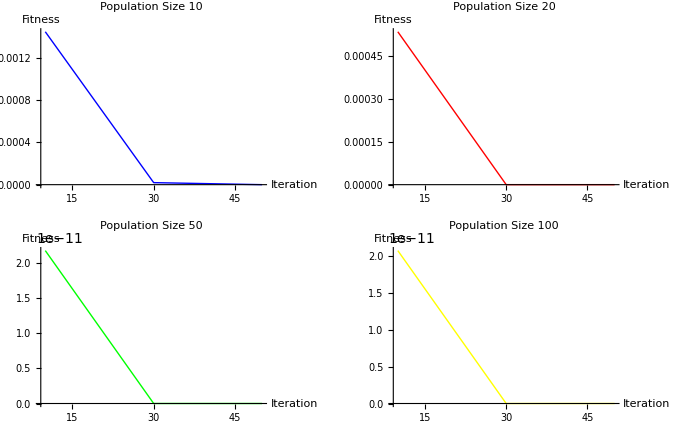

```mathematica
(*Filter data for dimension 2 and population size 10*)
spf210filteredData=Select[spfdata,#["Dimension"]==2&&#["Population Size"]==10&];
spf220filteredData=Select[spfdata,#["Dimension"]==2&&#["Population Size"]==20&];
spf250filteredData=Select[spfdata,#["Dimension"]==2&&#["Population Size"]==50&];
spf2100filteredData=Select[spfdata,#["Dimension"]==2&&#["Population Size"]==100&];
(*Extract iteration numbers and fitness values*)
spf210iterationNumbers=spf210filteredData[[All,"Iteration Number"]];
spf210fitnessValues=spf210filteredData[[All,"Fitness"]];
spf220iterationNumbers=spf220filteredData[[All,"Iteration Number"]];
spf220fitnessValues=spf220filteredData[[All,"Fitness"]];
spf250iterationNumbers=spf250filteredData[[All,"Iteration Number"]];
spf250fitnessValues=spf250filteredData[[All,"Fitness"]];
spf2100iterationNumbers=spf2100filteredData[[All,"Iteration Number"]];
spf2100fitnessValues=spf2100filteredData[[All,"Fitness"]];
(*Create the line plot*)
spf210Plot=ListLinePlot[Transpose[{spf210iterationNumbers,spf210fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Blue,Thick},PlotLabel->"Population Size 10",LabelStyle->{Bold,10}];
spf220Plot=ListLinePlot[Transpose[{spf220iterationNumbers,spf220fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Red,Thick},PlotLabel->"Population Size 20",LabelStyle->{Bold,10}];
spf250Plot=ListLinePlot[Transpose[{spf250iterationNumbers,spf250fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Green,Thick},PlotLabel->"Population Size 50",LabelStyle->{Bold,10}];
spf2100Plot=ListLinePlot[Transpose[{spf2100iterationNumbers,spf2100fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Yellow,Thick},PlotLabel->"Population Size 100",LabelStyle->{Bold,10}];

GraphicsGrid[{{Graphics[spf210Plot], Graphics[spf220Plot]}, 
 {Graphics[spf250Plot],Graphics[spf2100Plot]}},Frame->All]
```

```mathematica
(*Filter data for dimension 2*)
spf2dimension2Data=Select[spfdata,#["Dimension"]==2&];

(*Extract unique population sizes and iterations*)
spf2uniquePopulationSizes=Union[spf2dimension2Data[[All,"Population Size"]]];
spf2uniqueIterations=Union[spf2dimension2Data[[All,"Iteration Number"]]];

(*Function to create line plot for a specific iteration*)
spf2createLinePlot[iteration_]:=Module[{iterationData,sortedData},
(*Filter data for the specific iteration*)
iterationData=Select[spf2dimension2Data,#["Iteration Number"]==iteration&];
(*Sort data by population size to create a line plot*)
sortedData=SortBy[iterationData,#["Population Size"]&];
(*Extract population sizes and fitness values*)
spf2populationSizes=sortedData[[All,"Population Size"]];
spf2fitnessValues=sortedData[[All,"Fitness"]];
(*Create the line plot*)
ListLinePlot[Transpose[{spf2populationSizes,spf2fitnessValues}],PlotRange->All,AxesLabel->{"Population Size","Fitness"},PlotLabel->"Iteration: "<>ToString[iteration],ImageSize->Medium]]

(*Create frames for each unique iteration*)
spf2frames=Table[spf2createLinePlot[iteration],{iteration,spf2uniqueIterations}];

(*Create the animation*)
spf2itaanimation=ListAnimate[spf2frames,AnimationRate->1]
```

```mathematica
(*Filter data for dimension 2*)
spf2dimension2Data=Select[spfdata,#["Dimension"]==2&];

(*Extract unique population sizes and iterations*)
spf2uniquePopulationSizes=Union[spf2dimension2Data[[All,"Population Size"]]];
spf2uniqueIterations=Union[spf2dimension2Data[[All,"Iteration Number"]]];

(*Function to create line plot for a specific population size*)
spf2createLinePlot[populationSize_]:=Module[{populationData,sortedData},
(*Filter data for the specific population size*)
populationData=Select[spf2dimension2Data,#["Population Size"]==populationSize&];
(*Sort data by iteration number to create a line plot*)
sortedData=SortBy[populationData,#["Iteration Number"]&];
(*Extract iteration numbers and fitness values*)spf2iterations=sortedData[[All,"Iteration Number"]];
spf2fitnessValues=sortedData[[All,"Fitness"]];
(*Create the line plot*)ListLinePlot[Transpose[{spf2iterations,spf2fitnessValues}],PlotRange->All,AxesLabel->{"Iteration Number","Fitness"},PlotLabel->"Population Size: "<>ToString[populationSize],ImageSize->Medium]]

(*Create frames for each unique population size*)
spf2frames=Table[spf2createLinePlot[populationSize],{populationSize,spf2uniquePopulationSizes}];

(*Create the animation*)
spf2psanimation=ListAnimate[spf2frames,AnimationRate->1]
```

```mathematica
Export["spf2itaanimationgif.gif",spf2itaanimation]
Export["spf2itaanimationmp4.mp4",spf2itaanimation]
```

spf2itaanimationgif.gif

spf2itaanimationmp4.mp4

```mathematica
Export["spf2psanimationgif.gif",spf2psanimation]
Export["spf2psanimationmp4.mp4",spf2psanimation]
```

spf2psanimationgif.gif

spf2psanimationmp4.mp4

Dimension 05

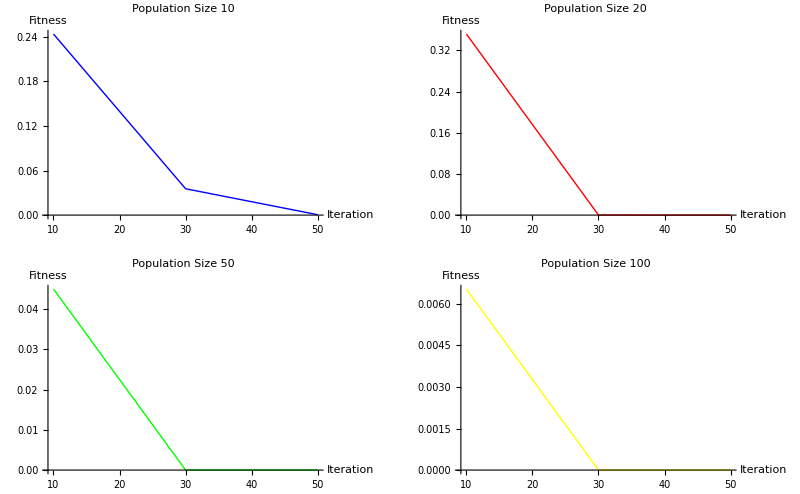

```mathematica
(*Filter data for dimension 5 and population size 10*)
spf510filteredData=Select[spfdata,#["Dimension"]==5&&#["Population Size"]==10&];
spf520filteredData=Select[spfdata,#["Dimension"]==5&&#["Population Size"]==20&];
spf550filteredData=Select[spfdata,#["Dimension"]==5&&#["Population Size"]==50&];
spf5100filteredData=Select[spfdata,#["Dimension"]==5&&#["Population Size"]==100&];
(*Extract iteration numbers and fitness values*)
spf510iterationNumbers=spf510filteredData[[All,"Iteration Number"]];
spf510fitnessValues=spf510filteredData[[All,"Fitness"]];
spf520iterationNumbers=spf520filteredData[[All,"Iteration Number"]];
spf520fitnessValues=spf520filteredData[[All,"Fitness"]];
spf550iterationNumbers=spf550filteredData[[All,"Iteration Number"]];
spf550fitnessValues=spf550filteredData[[All,"Fitness"]];
spf5100iterationNumbers=spf5100filteredData[[All,"Iteration Number"]];
spf5100fitnessValues=spf5100filteredData[[All,"Fitness"]];
(*Create the line plot*)
spf510Plot=ListLinePlot[Transpose[{spf510iterationNumbers,spf510fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Blue,Thick},PlotLabel->"Population Size 10",LabelStyle->{Bold,10}];
spf520Plot=ListLinePlot[Transpose[{spf520iterationNumbers,spf520fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Red,Thick},PlotLabel->"Population Size 20",LabelStyle->{Bold,10}];
spf550Plot=ListLinePlot[Transpose[{spf550iterationNumbers,spf550fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Green,Thick},PlotLabel->"Population Size 50",LabelStyle->{Bold,10}];
spf5100Plot=ListLinePlot[Transpose[{spf5100iterationNumbers,spf5100fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Yellow,Thick},PlotLabel->"Population Size 100",LabelStyle->{Bold,10}];

GraphicsGrid[{{Graphics[spf510Plot], Graphics[spf520Plot]}, 
 {Graphics[spf550Plot],Graphics[spf5100Plot]}},Frame->All]
```

```mathematica
(*Filter data for dimension 2*)
spf5dimension5Data=Select[spfdata,#["Dimension"]==5&];

(*Extract unique population sizes and iterations*)
spf5uniquePopulationSizes=Union[spf5dimension5Data[[All,"Population Size"]]];
spf5uniqueIterations=Union[spf5dimension5Data[[All,"Iteration Number"]]];

(*Function to create line plot for a specific iteration*)
spf5createLinePlot[iteration_]:=Module[{iterationData,sortedData},
(*Filter data for the specific iteration*)
iterationData=Select[spf5dimension5Data,#["Iteration Number"]==iteration&];
(*Sort data by population size to create a line plot*)
sortedData=SortBy[iterationData,#["Population Size"]&];
(*Extract population sizes and fitness values*)
spf5populationSizes=sortedData[[All,"Population Size"]];
spf5fitnessValues=sortedData[[All,"Fitness"]];
(*Create the line plot*)
ListLinePlot[Transpose[{spf5populationSizes,spf5fitnessValues}],PlotRange->All,AxesLabel->{"Population Size","Fitness"},PlotLabel->"Iteration: "<>ToString[iteration],ImageSize->Medium]]

(*Create frames for each unique iteration*)
spf5frames=Table[spf5createLinePlot[iteration],{iteration,spf5uniqueIterations}];

(*Create the animation*)
spf5itaanimation=ListAnimate[spf5frames,AnimationRate->1]
```

```mathematica
(*Filter data for dimension 2*)
spf5dimension5Data=Select[spfdata,#["Dimension"]==5&];

(*Extract unique population sizes and iterations*)
spf5uniquePopulationSizes=Union[spf5dimension5Data[[All,"Population Size"]]];
spf5uniqueIterations=Union[spf5dimension5Data[[All,"Iteration Number"]]];

(*Function to create line plot for a specific population size*)
spf5createLinePlot[populationSize_]:=Module[{populationData,sortedData},
(*Filter data for the specific population size*)
populationData=Select[spf5dimension5Data,#["Population Size"]==populationSize&];
(*Sort data by iteration number to create a line plot*)
sortedData=SortBy[populationData,#["Iteration Number"]&];
(*Extract iteration numbers and fitness values*)spf5iterations=sortedData[[All,"Iteration Number"]];
spf5fitnessValues=sortedData[[All,"Fitness"]];
(*Create the line plot*)ListLinePlot[Transpose[{spf5iterations,spf5fitnessValues}],PlotRange->All,AxesLabel->{"Iteration Number","Fitness"},PlotLabel->"Population Size: "<>ToString[populationSize],ImageSize->Medium]]

(*Create frames for each unique population size*)
spf5frames=Table[spf5createLinePlot[populationSize],{populationSize,spf5uniquePopulationSizes}];

(*Create the animation*)
spf5psanimation=ListAnimate[spf5frames,AnimationRate->1]
```

```mathematica
Export["spf5itaanimationgif.gif",spf5itaanimation]
Export["spf5itaanimationmp4.mp4",spf5itaanimation]
```

spf5itaanimationgif.gif

spf5itaanimationmp4.mp4

```mathematica
Export["spf5psanimationgif.gif",spf5psanimation]
Export["spf5psanimationmp4.mp4",spf5psanimation]
```

spf5psanimationgif.gif

spf5psanimationmp4.mp4

Dimension 10

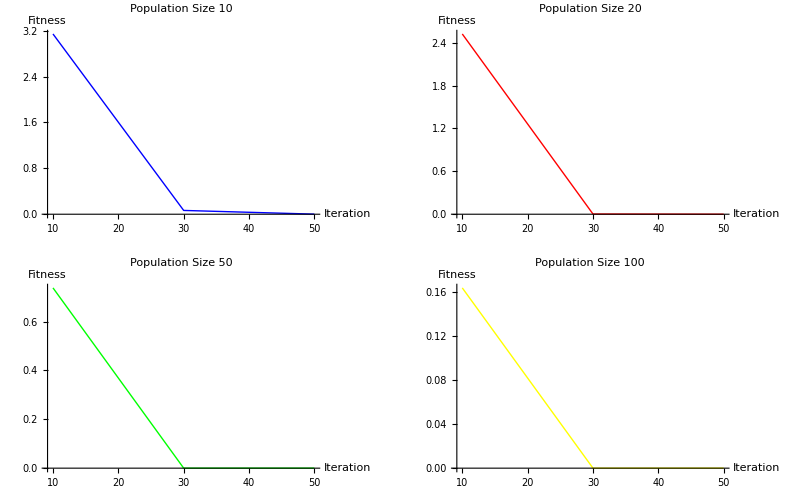

```mathematica
(*Filter data for dimension 10 and population size 10*)
spf1010filteredData=Select[spfdata,#["Dimension"]==10&&#["Population Size"]==10&];
spf1020filteredData=Select[spfdata,#["Dimension"]==10&&#["Population Size"]==20&];
spf1050filteredData=Select[spfdata,#["Dimension"]==10&&#["Population Size"]==50&];
spf10100filteredData=Select[spfdata,#["Dimension"]==10&&#["Population Size"]==100&];
(*Extract iteration numbers and fitness values*)
spf1010iterationNumbers=spf1010filteredData[[All,"Iteration Number"]];
spf1010fitnessValues=spf1010filteredData[[All,"Fitness"]];
spf1020iterationNumbers=spf1020filteredData[[All,"Iteration Number"]];
spf1020fitnessValues=spf1020filteredData[[All,"Fitness"]];
spf1050iterationNumbers=spf1050filteredData[[All,"Iteration Number"]];
spf1050fitnessValues=spf1050filteredData[[All,"Fitness"]];
spf10100iterationNumbers=spf10100filteredData[[All,"Iteration Number"]];
spf10100fitnessValues=spf10100filteredData[[All,"Fitness"]];
(*Create the line plot*)
spf1010Plot=ListLinePlot[Transpose[{spf1010iterationNumbers,spf1010fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Blue,Thick},PlotLabel->"Population Size 10",LabelStyle->{Bold,10}];
spf1020Plot=ListLinePlot[Transpose[{spf1020iterationNumbers,spf1020fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Red,Thick},PlotLabel->"Population Size 20",LabelStyle->{Bold,10}];
spf1050Plot=ListLinePlot[Transpose[{spf1050iterationNumbers,spf1050fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Green,Thick},PlotLabel->"Population Size 50",LabelStyle->{Bold,10}];
spf10100Plot=ListLinePlot[Transpose[{spf10100iterationNumbers,spf10100fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Yellow,Thick},PlotLabel->"Population Size 100",LabelStyle->{Bold,10}];

GraphicsGrid[{{Graphics[spf1010Plot], Graphics[spf1020Plot]}, 
 {Graphics[spf1050Plot],Graphics[spf10100Plot]}},Frame->All]
```

```mathematica
(*Filter data for dimension 10*)
spf10dimension10Data=Select[spfdata,#["Dimension"]==10&];

(*Extract unique population sizes and iterations*)
spf10uniquePopulationSizes=Union[spf10dimension10Data[[All,"Population Size"]]];
spf10uniqueIterations=Union[spf10dimension10Data[[All,"Iteration Number"]]];

(*Function to create line plot for a specific iteration*)
spf10createLinePlot[iteration_]:=Module[{iterationData,sortedData},
(*Filter data for the specific iteration*)
iterationData=Select[spf10dimension10Data,#["Iteration Number"]==iteration&];
(*Sort data by population size to create a line plot*)
sortedData=SortBy[iterationData,#["Population Size"]&];
(*Extract population sizes and fitness values*)
spf10populationSizes=sortedData[[All,"Population Size"]];
spf10fitnessValues=sortedData[[All,"Fitness"]];
(*Create the line plot*)
ListLinePlot[Transpose[{spf10populationSizes,spf10fitnessValues}],PlotRange->All,AxesLabel->{"Population Size","Fitness"},PlotLabel->"Iteration: "<>ToString[iteration],ImageSize->Medium]]

(*Create frames for each unique iteration*)
spf10frames=Table[spf10createLinePlot[iteration],{iteration,spf10uniqueIterations}];

(*Create the animation*)
spf10itaanimation=ListAnimate[spf10frames,AnimationRate->1]
```

```mathematica
(*Filter data for dimension 10*)
spf10dimension10Data=Select[spfdata,#["Dimension"]==10&];

(*Extract unique population sizes and iterations*)
spf10uniquePopulationSizes=Union[spf10dimension10Data[[All,"Population Size"]]];
spf10uniqueIterations=Union[spf10dimension10Data[[All,"Iteration Number"]]];

(*Function to create line plot for a specific population size*)
spf10createLinePlot[populationSize_]:=Module[{populationData,sortedData},
(*Filter data for the specific population size*)
populationData=Select[spf10dimension10Data,#["Population Size"]==populationSize&];
(*Sort data by iteration number to create a line plot*)
sortedData=SortBy[populationData,#["Iteration Number"]&];
(*Extract iteration numbers and fitness values*)spf10iterations=sortedData[[All,"Iteration Number"]];
spf10fitnessValues=sortedData[[All,"Fitness"]];
(*Create the line plot*)ListLinePlot[Transpose[{spf10iterations,spf10fitnessValues}],PlotRange->All,AxesLabel->{"Iteration Number","Fitness"},PlotLabel->"Population Size: "<>ToString[populationSize],ImageSize->Medium]]

(*Create frames for each unique population size*)
spf10frames=Table[spf10createLinePlot[populationSize],{populationSize,spf10uniquePopulationSizes}];

(*Create the animation*)
spf10psanimation=ListAnimate[spf10frames,AnimationRate->1]
```

```mathematica
Export["spf10itaanimationgif.gif",spf10itaanimation]
Export["spf10itaanimationmp4.mp4",spf10itaanimation]
```

spf10itaanimationgif.gif

spf10itaanimationmp4.mp4

```mathematica
Export["spf10psanimationgif.gif",spf10psanimation]
Export["spf10psanimationmp4.mp4",spf10psanimation]
```

spf10psanimationgif.gif

spf10psanimationmp4.mp4

Visualization for Rastrigin function

```mathematica
rafdata=Normal[rafDF];
```

Dimension 02

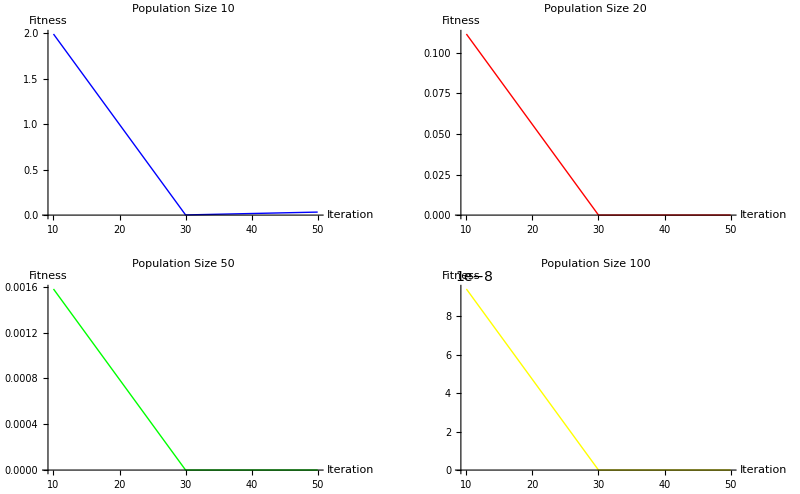

```mathematica
(*Filter data for dimension 2 and population size 10*)
raf210filteredData=Select[rafdata,#["Dimension"]==2&&#["Population Size"]==10&];
raf220filteredData=Select[rafdata,#["Dimension"]==2&&#["Population Size"]==20&];
raf250filteredData=Select[rafdata,#["Dimension"]==2&&#["Population Size"]==50&];
raf2100filteredData=Select[rafdata,#["Dimension"]==2&&#["Population Size"]==100&];
(*Extract iteration numbers and fitness values*)
raf210iterationNumbers=raf210filteredData[[All,"Iteration Number"]];
raf210fitnessValues=raf210filteredData[[All,"Fitness"]];
raf220iterationNumbers=raf220filteredData[[All,"Iteration Number"]];
raf220fitnessValues=raf220filteredData[[All,"Fitness"]];
raf250iterationNumbers=raf250filteredData[[All,"Iteration Number"]];
raf250fitnessValues=raf250filteredData[[All,"Fitness"]];
raf2100iterationNumbers=raf2100filteredData[[All,"Iteration Number"]];
raf2100fitnessValues=raf2100filteredData[[All,"Fitness"]];
(*Create the line plot*)
raf210Plot=ListLinePlot[Transpose[{raf210iterationNumbers,raf210fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Blue,Thick},PlotLabel->"Population Size 10",LabelStyle->{Bold,10}];
raf220Plot=ListLinePlot[Transpose[{raf220iterationNumbers,raf220fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Red,Thick},PlotLabel->"Population Size 20",LabelStyle->{Bold,10}];
raf250Plot=ListLinePlot[Transpose[{raf250iterationNumbers,raf250fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Green,Thick},PlotLabel->"Population Size 50",LabelStyle->{Bold,10}];
raf2100Plot=ListLinePlot[Transpose[{raf2100iterationNumbers,raf2100fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Yellow,Thick},PlotLabel->"Population Size 100",LabelStyle->{Bold,10}];

GraphicsGrid[{{Graphics[raf210Plot], Graphics[raf220Plot]}, 
 {Graphics[raf250Plot],Graphics[raf2100Plot]}},Frame->All]
```

```mathematica
(*Filter data for dimension 2*)
raf2dimension2Data=Select[rafdata,#["Dimension"]==2&];

(*Extract unique population sizes and iterations*)
raf2uniquePopulationSizes=Union[raf2dimension2Data[[All,"Population Size"]]];
raf2uniqueIterations=Union[raf2dimension2Data[[All,"Iteration Number"]]];

(*Function to create line plot for a specific iteration*)
raf2createLinePlot[iteration_]:=Module[{iterationData,sortedData},
(*Filter data for the specific iteration*)
iterationData=Select[raf2dimension2Data,#["Iteration Number"]==iteration&];
(*Sort data by population size to create a line plot*)
sortedData=SortBy[iterationData,#["Population Size"]&];
(*Extract population sizes and fitness values*)
raf2populationSizes=sortedData[[All,"Population Size"]];
raf2fitnessValues=sortedData[[All,"Fitness"]];
(*Create the line plot*)
ListLinePlot[Transpose[{raf2populationSizes,raf2fitnessValues}],PlotRange->All,AxesLabel->{"Population Size","Fitness"},PlotLabel->"Iteration: "<>ToString[iteration],ImageSize->Medium]]

(*Create frames for each unique iteration*)
raf2frames=Table[raf2createLinePlot[iteration],{iteration,raf2uniqueIterations}];

(*Create the animation*)
raf2itaanimation=ListAnimate[raf2frames,AnimationRate->1]
```

```mathematica
(*Filter data for dimension 2*)
raf2dimension2Data=Select[rafdata,#["Dimension"]==2&];

(*Extract unique population sizes and iterations*)
raf2uniquePopulationSizes=Union[raf2dimension2Data[[All,"Population Size"]]];
raf2uniqueIterations=Union[raf2dimension2Data[[All,"Iteration Number"]]];

(*Function to create line plot for a specific population size*)
raf2createLinePlot[populationSize_]:=Module[{populationData,sortedData},
(*Filter data for the specific population size*)
populationData=Select[raf2dimension2Data,#["Population Size"]==populationSize&];
(*Sort data by iteration number to create a line plot*)
sortedData=SortBy[populationData,#["Iteration Number"]&];
(*Extract iteration numbers and fitness values*)raf2iterations=sortedData[[All,"Iteration Number"]];
raf2fitnessValues=sortedData[[All,"Fitness"]];
(*Create the line plot*)ListLinePlot[Transpose[{raf2iterations,raf2fitnessValues}],PlotRange->All,AxesLabel->{"Iteration Number","Fitness"},PlotLabel->"Population Size: "<>ToString[populationSize],ImageSize->Medium]]

(*Create frames for each unique population size*)
raf2frames=Table[raf2createLinePlot[populationSize],{populationSize,raf2uniquePopulationSizes}];

(*Create the animation*)
raf2psanimation=ListAnimate[raf2frames,AnimationRate->1]
```

```mathematica
Export["raf2itaanimationgif.gif",raf2itaanimation]
Export["raf2itaanimationmp4.mp4",raf2itaanimation]
```

raf2itaanimationgif.gif

raf2itaanimationmp4.mp4

```mathematica
Export["raf2psanimationgif.gif",raf2psanimation]
Export["raf2psanimationmp4.mp4",raf2psanimation]
```

raf2psanimationgif.gif

raf2psanimationmp4.mp4

Dimension 05

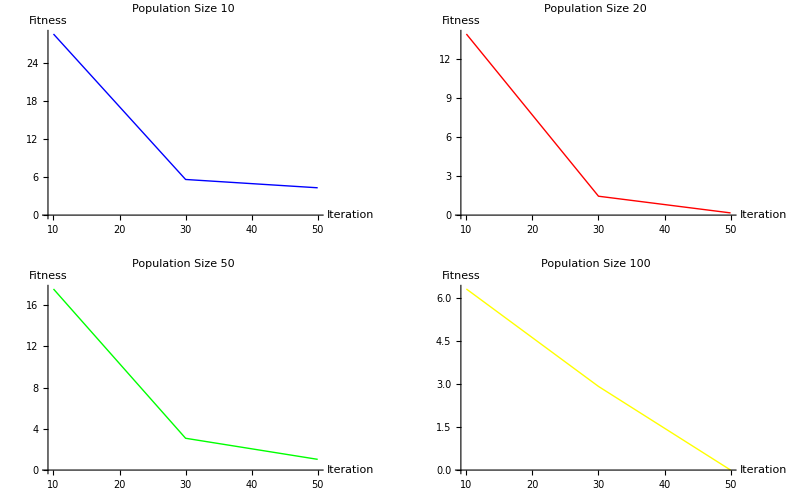

```mathematica
(*Filter data for dimension 5 and population size 10*)
raf510filteredData=Select[rafdata,#["Dimension"]==5&&#["Population Size"]==10&];
raf520filteredData=Select[rafdata,#["Dimension"]==5&&#["Population Size"]==20&];
raf550filteredData=Select[rafdata,#["Dimension"]==5&&#["Population Size"]==50&];
raf5100filteredData=Select[rafdata,#["Dimension"]==5&&#["Population Size"]==100&];
(*Extract iteration numbers and fitness values*)
raf510iterationNumbers=raf510filteredData[[All,"Iteration Number"]];
raf510fitnessValues=raf510filteredData[[All,"Fitness"]];
raf520iterationNumbers=raf520filteredData[[All,"Iteration Number"]];
raf520fitnessValues=raf520filteredData[[All,"Fitness"]];
raf550iterationNumbers=raf550filteredData[[All,"Iteration Number"]];
raf550fitnessValues=raf550filteredData[[All,"Fitness"]];
raf5100iterationNumbers=raf5100filteredData[[All,"Iteration Number"]];
raf5100fitnessValues=raf5100filteredData[[All,"Fitness"]];
(*Create the line plot*)
raf510Plot=ListLinePlot[Transpose[{raf510iterationNumbers,raf510fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Blue,Thick},PlotLabel->"Population Size 10",LabelStyle->{Bold,10}];
raf520Plot=ListLinePlot[Transpose[{raf520iterationNumbers,raf520fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Red,Thick},PlotLabel->"Population Size 20",LabelStyle->{Bold,10}];
raf550Plot=ListLinePlot[Transpose[{raf550iterationNumbers,raf550fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Green,Thick},PlotLabel->"Population Size 50",LabelStyle->{Bold,10}];
raf5100Plot=ListLinePlot[Transpose[{raf5100iterationNumbers,raf5100fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Yellow,Thick},PlotLabel->"Population Size 100",LabelStyle->{Bold,10}];

GraphicsGrid[{{Graphics[raf510Plot], Graphics[raf520Plot]}, 
 {Graphics[raf550Plot],Graphics[raf5100Plot]}},Frame->All]
```

```mathematica
(*Filter data for dimension 2*)
raf5dimension5Data=Select[rafdata,#["Dimension"]==5&];

(*Extract unique population sizes and iterations*)
raf5uniquePopulationSizes=Union[raf5dimension5Data[[All,"Population Size"]]];
raf5uniqueIterations=Union[raf5dimension5Data[[All,"Iteration Number"]]];

(*Function to create line plot for a specific iteration*)
raf5createLinePlot[iteration_]:=Module[{iterationData,sortedData},
(*Filter data for the specific iteration*)
iterationData=Select[raf5dimension5Data,#["Iteration Number"]==iteration&];
(*Sort data by population size to create a line plot*)
sortedData=SortBy[iterationData,#["Population Size"]&];
(*Extract population sizes and fitness values*)
raf5populationSizes=sortedData[[All,"Population Size"]];
raf5fitnessValues=sortedData[[All,"Fitness"]];
(*Create the line plot*)
ListLinePlot[Transpose[{raf5populationSizes,raf5fitnessValues}],PlotRange->All,AxesLabel->{"Population Size","Fitness"},PlotLabel->"Iteration: "<>ToString[iteration],ImageSize->Medium]]

(*Create frames for each unique iteration*)
raf5frames=Table[raf5createLinePlot[iteration],{iteration,raf5uniqueIterations}];

(*Create the animation*)
raf5itaanimation=ListAnimate[raf5frames,AnimationRate->1]
```

```mathematica
(*Filter data for dimension 2*)
raf5dimension5Data=Select[rafdata,#["Dimension"]==5&];

(*Extract unique population sizes and iterations*)
raf5uniquePopulationSizes=Union[raf5dimension5Data[[All,"Population Size"]]];
raf5uniqueIterations=Union[raf5dimension5Data[[All,"Iteration Number"]]];

(*Function to create line plot for a specific population size*)
raf5createLinePlot[populationSize_]:=Module[{populationData,sortedData},
(*Filter data for the specific population size*)
populationData=Select[raf5dimension5Data,#["Population Size"]==populationSize&];
(*Sort data by iteration number to create a line plot*)
sortedData=SortBy[populationData,#["Iteration Number"]&];
(*Extract iteration numbers and fitness values*)raf5iterations=sortedData[[All,"Iteration Number"]];
raf5fitnessValues=sortedData[[All,"Fitness"]];
(*Create the line plot*)ListLinePlot[Transpose[{raf5iterations,raf5fitnessValues}],PlotRange->All,AxesLabel->{"Iteration Number","Fitness"},PlotLabel->"Population Size: "<>ToString[populationSize],ImageSize->Medium]]

(*Create frames for each unique population size*)
raf5frames=Table[raf5createLinePlot[populationSize],{populationSize,raf5uniquePopulationSizes}];

(*Create the animation*)
raf5psanimation=ListAnimate[raf5frames,AnimationRate->1]
```

```mathematica
Export["raf5itaanimationgif.gif",raf5itaanimation]
Export["raf5itaanimationmp4.mp4",raf5itaanimation]
```

raf5itaanimationgif.gif

raf5itaanimationmp4.mp4

```mathematica
Export["raf5psanimationgif.gif",raf5psanimation]
Export["raf5psanimationmp4.mp4",raf5psanimation]
```

raf5psanimationgif.gif

raf5psanimationmp4.mp4

Visualization for Rosenbrock function

```mathematica
rbfdata=Normal[rbfDF];
```

Dimension 02

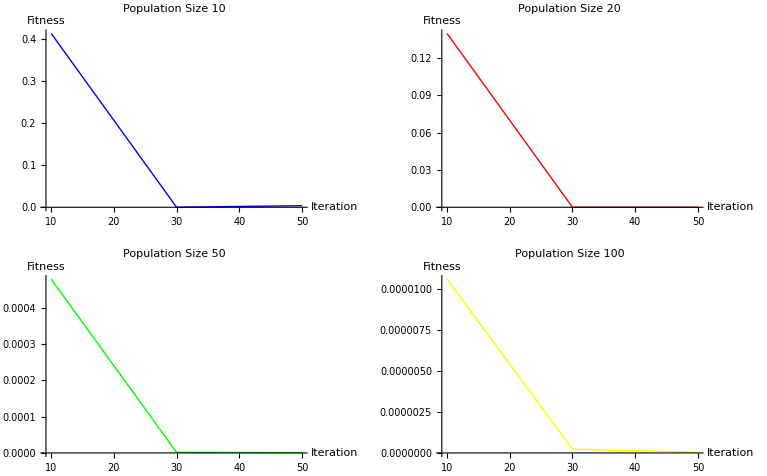

```mathematica
(*Filter data for dimension 2 and population size 10*)
rbf210filteredData=Select[rbfdata,#["Dimension"]==2&&#["Population Size"]==10&];
rbf220filteredData=Select[rbfdata,#["Dimension"]==2&&#["Population Size"]==20&];
rbf250filteredData=Select[rbfdata,#["Dimension"]==2&&#["Population Size"]==50&];
rbf2100filteredData=Select[rbfdata,#["Dimension"]==2&&#["Population Size"]==100&];
(*Extract iteration numbers and fitness values*)
rbf210iterationNumbers=rbf210filteredData[[All,"Iteration Number"]];
rbf210fitnessValues=rbf210filteredData[[All,"Fitness"]];
rbf220iterationNumbers=rbf220filteredData[[All,"Iteration Number"]];
rbf220fitnessValues=rbf220filteredData[[All,"Fitness"]];
rbf250iterationNumbers=rbf250filteredData[[All,"Iteration Number"]];
rbf250fitnessValues=rbf250filteredData[[All,"Fitness"]];
rbf2100iterationNumbers=rbf2100filteredData[[All,"Iteration Number"]];
rbf2100fitnessValues=rbf2100filteredData[[All,"Fitness"]];
(*Create the line plot*)
rbf210Plot=ListLinePlot[Transpose[{rbf210iterationNumbers,rbf210fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Blue,Thick},PlotLabel->"Population Size 10",LabelStyle->{Bold,10}];
rbf220Plot=ListLinePlot[Transpose[{rbf220iterationNumbers,rbf220fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Red,Thick},PlotLabel->"Population Size 20",LabelStyle->{Bold,10}];
rbf250Plot=ListLinePlot[Transpose[{rbf250iterationNumbers,rbf250fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Green,Thick},PlotLabel->"Population Size 50",LabelStyle->{Bold,10}];
rbf2100Plot=ListLinePlot[Transpose[{rbf2100iterationNumbers,rbf2100fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Yellow,Thick},PlotLabel->"Population Size 100",LabelStyle->{Bold,10}];

GraphicsGrid[{{Graphics[rbf210Plot], Graphics[rbf220Plot]}, 
 {Graphics[rbf250Plot],Graphics[rbf2100Plot]}},Frame->All]
```

```mathematica
(*Filter data for dimension 2*)
rbf2dimension2Data=Select[rbfdata,#["Dimension"]==2&];

(*Extract unique population sizes and iterations*)
rbf2uniquePopulationSizes=Union[rbf2dimension2Data[[All,"Population Size"]]];
rbf2uniqueIterations=Union[rbf2dimension2Data[[All,"Iteration Number"]]];

(*Function to create line plot for a specific iteration*)
rbf2createLinePlot[iteration_]:=Module[{iterationData,sortedData},
(*Filter data for the specific iteration*)
iterationData=Select[rbf2dimension2Data,#["Iteration Number"]==iteration&];
(*Sort data by population size to create a line plot*)
sortedData=SortBy[iterationData,#["Population Size"]&];
(*Extract population sizes and fitness values*)
rbf2populationSizes=sortedData[[All,"Population Size"]];
rbf2fitnessValues=sortedData[[All,"Fitness"]];
(*Create the line plot*)
ListLinePlot[Transpose[{rbf2populationSizes,rbf2fitnessValues}],PlotRange->All,AxesLabel->{"Population Size","Fitness"},PlotLabel->"Iteration: "<>ToString[iteration],ImageSize->Medium]]

(*Create frames for each unique iteration*)
rbf2frames=Table[rbf2createLinePlot[iteration],{iteration,rbf2uniqueIterations}];

(*Create the animation*)
rbf2itaanimation=ListAnimate[rbf2frames,AnimationRate->1]
```

```mathematica
(*Filter data for dimension 2*)
rbf2dimension2Data=Select[rbfdata,#["Dimension"]==2&];

(*Extract unique population sizes and iterations*)
rbf2uniquePopulationSizes=Union[rbf2dimension2Data[[All,"Population Size"]]];
rbf2uniqueIterations=Union[rbf2dimension2Data[[All,"Iteration Number"]]];

(*Function to create line plot for a specific population size*)
rbf2createLinePlot[populationSize_]:=Module[{populationData,sortedData},
(*Filter data for the specific population size*)
populationData=Select[rbf2dimension2Data,#["Population Size"]==populationSize&];
(*Sort data by iteration number to create a line plot*)
sortedData=SortBy[populationData,#["Iteration Number"]&];
(*Extract iteration numbers and fitness values*)rbf2iterations=sortedData[[All,"Iteration Number"]];
rbf2fitnessValues=sortedData[[All,"Fitness"]];
(*Create the line plot*)ListLinePlot[Transpose[{rbf2iterations,rbf2fitnessValues}],PlotRange->All,AxesLabel->{"Iteration Number","Fitness"},PlotLabel->"Population Size: "<>ToString[populationSize],ImageSize->Medium]]

(*Create frames for each unique population size*)
rbf2frames=Table[rbf2createLinePlot[populationSize],{populationSize,rbf2uniquePopulationSizes}];

(*Create the animation*)
rbf2psanimation=ListAnimate[rbf2frames,AnimationRate->1]
```

```mathematica
Export["rbf2itaanimationgif.gif",rbf2itaanimation]
Export["rbf2itaanimationmp4.mp4",rbf2itaanimation]
```

rbf2itaanimationgif.gif

rbf2itaanimationmp4.mp4

```mathematica
Export["rbf2psanimationgif.gif",rbf2psanimation]
Export["rbf2psanimationmp4.mp4",rbf2psanimation]
```

rbf2psanimationgif.gif

rbf2psanimationmp4.mp4

Dimension 05

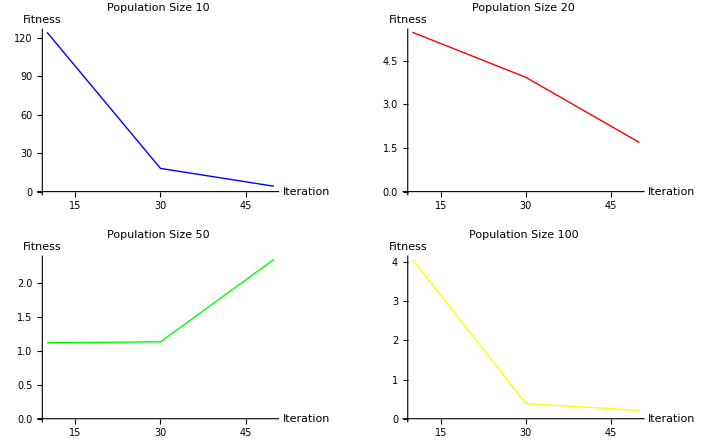

```mathematica
(*Filter data for dimension 5 and population size 10*)
rbf510filteredData=Select[rbfdata,#["Dimension"]==5&&#["Population Size"]==10&];
rbf520filteredData=Select[rbfdata,#["Dimension"]==5&&#["Population Size"]==20&];
rbf550filteredData=Select[rbfdata,#["Dimension"]==5&&#["Population Size"]==50&];
rbf5100filteredData=Select[rbfdata,#["Dimension"]==5&&#["Population Size"]==100&];
(*Extract iteration numbers and fitness values*)
rbf510iterationNumbers=rbf510filteredData[[All,"Iteration Number"]];
rbf510fitnessValues=rbf510filteredData[[All,"Fitness"]];
rbf520iterationNumbers=rbf520filteredData[[All,"Iteration Number"]];
rbf520fitnessValues=rbf520filteredData[[All,"Fitness"]];
rbf550iterationNumbers=rbf550filteredData[[All,"Iteration Number"]];
rbf550fitnessValues=rbf550filteredData[[All,"Fitness"]];
rbf5100iterationNumbers=rbf5100filteredData[[All,"Iteration Number"]];
rbf5100fitnessValues=rbf5100filteredData[[All,"Fitness"]];
(*Create the line plot*)
rbf510Plot=ListLinePlot[Transpose[{rbf510iterationNumbers,rbf510fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Blue,Thick},PlotLabel->"Population Size 10",LabelStyle->{Bold,10}];
rbf520Plot=ListLinePlot[Transpose[{rbf520iterationNumbers,rbf520fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Red,Thick},PlotLabel->"Population Size 20",LabelStyle->{Bold,10}];
rbf550Plot=ListLinePlot[Transpose[{rbf550iterationNumbers,rbf550fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Green,Thick},PlotLabel->"Population Size 50",LabelStyle->{Bold,10}];
rbf5100Plot=ListLinePlot[Transpose[{rbf5100iterationNumbers,rbf5100fitnessValues}],PlotRange->All,AxesLabel->{"Iteration","Fitness"},PlotStyle->{Yellow,Thick},PlotLabel->"Population Size 100",LabelStyle->{Bold,10}];

GraphicsGrid[{{Graphics[rbf510Plot], Graphics[rbf520Plot]}, 
 {Graphics[rbf550Plot],Graphics[rbf5100Plot]}},Frame->All]
```

```mathematica
(*Filter data for dimension 2*)
rbf5dimension5Data=Select[rbfdata,#["Dimension"]==5&];

(*Extract unique population sizes and iterations*)
rbf5uniquePopulationSizes=Union[rbf5dimension5Data[[All,"Population Size"]]];
rbf5uniqueIterations=Union[rbf5dimension5Data[[All,"Iteration Number"]]];

(*Function to create line plot for a specific iteration*)
rbf5createLinePlot[iteration_]:=Module[{iterationData,sortedData},
(*Filter data for the specific iteration*)
iterationData=Select[rbf5dimension5Data,#["Iteration Number"]==iteration&];
(*Sort data by population size to create a line plot*)
sortedData=SortBy[iterationData,#["Population Size"]&];
(*Extract population sizes and fitness values*)
rbf5populationSizes=sortedData[[All,"Population Size"]];
rbf5fitnessValues=sortedData[[All,"Fitness"]];
(*Create the line plot*)
ListLinePlot[Transpose[{rbf5populationSizes,rbf5fitnessValues}],PlotRange->All,AxesLabel->{"Population Size","Fitness"},PlotLabel->"Iteration: "<>ToString[iteration],ImageSize->Medium]]

(*Create frames for each unique iteration*)
rbf5frames=Table[rbf5createLinePlot[iteration],{iteration,rbf5uniqueIterations}];

(*Create the animation*)
rbf5itaanimation=ListAnimate[rbf5frames,AnimationRate->1]
```

```mathematica
(*Filter data for dimension 2*)
rbf5dimension5Data=Select[rbfdata,#["Dimension"]==5&];

(*Extract unique population sizes and iterations*)
rbf5uniquePopulationSizes=Union[rbf5dimension5Data[[All,"Population Size"]]];
rbf5uniqueIterations=Union[rbf5dimension5Data[[All,"Iteration Number"]]];

(*Function to create line plot for a specific population size*)
rbf5createLinePlot[populationSize_]:=Module[{populationData,sortedData},
(*Filter data for the specific population size*)
populationData=Select[rbf5dimension5Data,#["Population Size"]==populationSize&];
(*Sort data by iteration number to create a line plot*)
sortedData=SortBy[populationData,#["Iteration Number"]&];
(*Extract iteration numbers and fitness values*)rbf5iterations=sortedData[[All,"Iteration Number"]];
rbf5fitnessValues=sortedData[[All,"Fitness"]];
(*Create the line plot*)ListLinePlot[Transpose[{rbf5iterations,rbf5fitnessValues}],PlotRange->All,AxesLabel->{"Iteration Number","Fitness"},PlotLabel->"Population Size: "<>ToString[populationSize],ImageSize->Medium]]

(*Create frames for each unique population size*)
rbf5frames=Table[rbf5createLinePlot[populationSize],{populationSize,rbf5uniquePopulationSizes}];

(*Create the animation*)
rbf5psanimation=ListAnimate[rbf5frames,AnimationRate->1]
```

```mathematica
Export["rbf5itaanimationgif.gif",rbf5itaanimation]
Export["rbf5itaanimationmp4.mp4",rbf5itaanimation]
```

rbf5itaanimationgif.gif

rbf5itaanimationmp4.mp4

```mathematica
Export["rbf5psanimationgif.gif",rbf5psanimation]
Export["rbf5psanimationmp4.mp4",rbf5psanimation]
```

rbf5psanimationgif.gif

rbf5psanimationmp4.mp4